# Dendritic bistability supports order-selective synaptic input detection

Kyrus R. Mama, Kwabena A. Boahen

Code used to generate the figures in the manuscript “Dendritic bistability supports order-selective synaptic input detection”. 
Instructions: To reproduce a figure, run the initialization cells and then within the corresponding section, run code sequentially.
Runtime: Most figures generate near instantaneously. The parameter sweeps, especially those in 3D can take several hours though. Code used to save and load the results of each sweep is included. 
Version: This code was written and run in Wolfram version 14.2.1.0, on macOS 26.3. 
For further information on models implemented to generate the figures in the paper, refer to the methods section.

## Setup

Locate figure results and plots. savePanel exports a formatted panel; savePanels saves and displays the panels produced by a calculation.

```mathematica
paperRoot=ParentDirectory[NotebookDirectory[]];SetDirectory[paperRoot];figureFolder[n_]:=FileNameJoin[{paperRoot,"Figure"<>ToString[n]}];supplementFolder[n_]:=FileNameJoin[{paperRoot,"SupplementaryFigure"<>ToString[n]}];figureData[n_]:="results";Do[If[!DirectoryQ[FileNameJoin[{figureFolder[n],"plots"}]],CreateDirectory[FileNameJoin[{figureFolder[n],"plots"}],CreateIntermediateDirectories->True]],{n,1,8}];savePanel[folder_,name_,panel_]:=Module[{directory,filename,extension},directory=FileNameJoin[{folder,"plots"}];If[!DirectoryQ[directory],CreateDirectory[directory,CreateIntermediateDirectories->True]];extension=FileExtension[name];If[extension=="",extension=If[Head[panel]===Graphics3D,"png","svg"]];filename=If[FileExtension[name]=="",name<>"."<>extension,name];If[extension=="png"&&Head[panel]===Graphics3D,Export[FileNameJoin[{directory,filename}],Rasterize[panel,"Image",RasterSize->3000,Background->White],"PNG"],Export[FileNameJoin[{directory,filename}],panel,ToUpperCase[extension]]];panel];SetAttributes[savePanels,HoldRest];savePanels::count="Expected `1` panels; the calculation produced `2`.";savePanels[names_List,calculation_]:=Module[{generatedPanels={},value,number,folder},value=Block[{Print=Function[generatedPanel,AppendTo[generatedPanels,generatedPanel];]},calculation];generatedPanels=Select[generatedPanels,MatchQ[#1,_Graphics|_Graphics3D|_Grid|_Row]&];If[MatchQ[value,_Graphics|_Graphics3D|_Grid|_Row],AppendTo[generatedPanels,value]];If[Length[generatedPanels]≠Length[names],Message[savePanels::count,Length[names],Length[generatedPanels]];Return[$Failed]];Do[number=ToExpression[First[StringCases[names⟦i⟧,DigitCharacter..]]];folder=If[StringStartsQ[names⟦i⟧,"FigS"],supplementFolder[number],figureFolder[number]];savePanel[folder,names⟦i⟧,generatedPanels⟦i⟧],{i,Length[names]}];If[Length[generatedPanels]==1,First[generatedPanels],Column[generatedPanels]]];
```

Channel currents, voltage normalization and numerical helpers.

### Channel properties

Defines the voltage-dependent NMDA and GIRK currents and the transient AMPA current used throughout the model.

#### Voltage Scaling: mVto[v], tomV[vv], hato[𝓊𝒽𝒶]:

Normalizes voltages from E_GIRK and E_NMDA to -1 and 1.

mVto and tomV convert between millivolts and normalized voltage. hato converts a voltage slope to the normalized scale.

```mathematica
mVto[v_] :=
  2 * ((v - Subscript[NE, GIRK]) / (Subscript[NE, NMDA] - Subscript[NE, GIRK])) - 1;

tomV[vv_] :=
  (Subscript[NE, NMDA] - Subscript[NE, GIRK]) * ((vv + 1) / 2) + Subscript[NE, GIRK];

hato[v_] :=
  2 * (v / (Subscript[NE, NMDA] - Subscript[NE, GIRK]));
```

#### Sigmoidal activation: f_sig[v,e,vha,vs]:

Channel current per unit conductance, with slope parameter vs and midpoint vha; conductance is normalized to one at e, its reversal potential (Boahen 2022).

Define a sigmoid-gated current whose conductance equals one at its reversal potential.

```mathematica
Subscript[f, sig][v_,e_,vha_,vs_]:=(1+ⅇ^(-(e-vha)/vs))/(1+ⅇ^(-(v-vha)/vs))(e-v)
```

#### NMDA Parameters: NE_NMDA, 𝓊𝒽𝒶_NMDA, 𝓊𝓈_NMDA:

Set the NMDA reversal potential, voltage-gating midpoint and slope, then convert them to normalized voltage.

```mathematica
Subscript[NE, NMDA] = 0 * mV;

Subscript[uha, NMDA] = (-237/10) * mV;

Subscript[us, NMDA] = (125/10) * mV;

Subscript[e, NMDA] = mVto[Subscript[NE, NMDA]];

Subscript[𝓊𝒽𝒶, NMDA] = mVto[Subscript[uha, NMDA]]; Subscript[𝓊𝓈, NMDA] = hato[Subscript[us, NMDA]];
```

#### GIRK Parameters: NE_GIRK, us_GIRK, uha_GIRK:

Set the GIRK reversal potential, voltage-dependence midpoint and slope, then convert them to normalized voltage.

```mathematica
Subscript[NE, GIRK] = -90 * mV;

Subscript[uha, GIRK] = -80 * mV;

Subscript[us, GIRK] = -10 * mV;

Subscript[e, GIRK] = mVto[Subscript[NE, GIRK]];

Subscript[𝓊𝒽𝒶, GIRK] = mVto[Subscript[uha, GIRK]]; Subscript[𝓊𝓈, GIRK] = hato[Subscript[us, GIRK]];
```

#### NMDA and GIRK current per unit conductance:

Define NMDA and GIRK currents using their normalized voltage-gating parameters.

```mathematica
Subscript[f, NMDA][ux_]:=Subscript[f, sig][ux,Subscript[e, NMDA],Subscript[𝓊𝒽𝒶, NMDA],Subscript[𝓊𝓈, NMDA]]
Subscript[f, GIRK][ux_]:=Subscript[f, sig][ux,Subscript[e, GIRK],Subscript[𝓊𝒽𝒶, GIRK],Subscript[𝓊𝓈, GIRK]]
```

Define the cubic current with resting and plateauing equilibria at −1 and +1.

```mathematica
𝒻[ux_]:=-1/2(ux-1)(ux+1)(ux+𝓇);
```

where 𝓇=Δ𝒢_c/(2 𝒢_c)

#### Alpha function and Dirac delta approximations

Define a finite-width approximation to a Dirac delta and a unit-height rectangular input.

```mathematica
δ[d_]:=(UnitStep[(#+d/2)]-UnitStep[(#-d/2)])/d&;
ι[d_]:=UnitStep[(#+d/2)]-UnitStep[(#-d/2)]&;
```

Define an AMPA alpha function with unit peak and zero activation before onset.

```mathematica
α[τ_]:=(UnitStep[#])(#/τ ⅇ^((-(#-τ))/τ))&
```

#### AMPA channel current per unit conductance

Multiply the AMPA alpha function by the normalized driving voltage.

```mathematica
Subscript[f, AMPA][u_,t_,τAMPA_,t0_]:=α[τAMPA][t-t0] (1-u);
```

### Sweeping helper functions

Routines used to sweep parameter space efficiently.

recfuncsolND refines a sampled grid and evaluates unresolved points. theCut repeats this step across the specified parameter ranges. plotCutBoundary2d draws boundaries between the resulting classes.

```mathematica
PlotCutBoundary::dims = "Expected a two-dimensional grid."; recfuncsolND[vals_, coords_, func_, possible_,
   depth_, mindepth_] :=
  Module[{curDim, newDim, newVals, newCoords, result},
    curDim = Dimensions[vals];
    newDim = (2 * #1 - 1&) /@ curDim;
    newVals = ArrayResample[vals, newDim];
    newCoords = ArrayResample[coords, Append[newDim, Length[curDim]]];
    result =
      MapThread[
        Function[{val, coordVec},
          If[(MemberQ[possible, val] && depth > mindepth) || depth < mindepth,
            val
            ,
            func @@ coordVec
          ]
        ]
        ,
        {newVals, newCoords}
        ,
        Length[curDim]
      ];
    {result, newCoords}
  ]; theCut[f_, varRanges_, minDepth_, maxDepth_, possibilities_] :=
  Module[{n, boundaries, dims, corners, initialVals, vals, coords},
    n = Length[varRanges];
    boundaries = varRanges[[All, {2, 3}]];
    dims = ConstantArray[2, n];
    corners = Tuples[boundaries];
    initialVals = (f @@ #1&) /@ corners;
    vals = ArrayReshape[initialVals, dims];
    coords = ArrayReshape[corners, Append[dims, n]];
    Do[
      Print[d];
      {vals, coords} = recfuncsolND[vals, coords, f, possibilities, d, minDepth]
      ,
      {d, 2, maxDepth}
    ];
    {vals, coords}
  ]; plotCutBoundary2d[{vals_, _}, varRanges_, possibilities_, colors_ : {Green, White}, contourStyleT_
    :Thick] :=
  Module[{n, dr, names, m, codeRules, codeVals, isos},
    n = Length[varRanges];
    dr = varRanges[[All, {2, 3}]];
    names = varRanges[[All, 1]];
    m = Length[possibilities];
    codeRules = Thread[possibilities -> Range[m]];
    codeVals = vals /. codeRules;
    isos = Range[1.5, m, 1];
    Switch[n,
      2,
        codeVals = Transpose[codeVals, {2, 1}];
        ListContourPlot[codeVals, Contours -> isos, ContourStyle -> contourStyleT, DataRange -> dr, Frame
           -> True, FrameLabel -> names, PlotRange -> All, PlotTheme -> "Detailed", Mesh -> None, ContourShading
           -> colors, PlotLegends -> None]
      ,
      _,
        Message[PlotCutBoundary::dims, n];
        $Failed
    ]
  ];
```

## IV curves

Computes the current-voltage curve that underlies the model’s bistability. Shows how coactive depolarizing (𝒢_NMDA) and hyperpolarizing (𝒢_GIRK) conductances shape the fixed-point structure of a dendritic segment.

### Fig. 2 IV curves

Shows how NMDA and GIRK conductances together make a segment bistable, with stable rest and plateau states separated by threshold. Also compares the sigmoidal channel model with the cubic approximation used to analyze front propagation.

𝒢_NMDA=3/5 𝒢_c and 𝒢_GIRK=7/5 𝒢_c gives Δ𝒢_c/(2 𝒢_c)=(𝒢_NMDA-𝒢_GIRK)/(𝒢_NMDA+𝒢_GIRK)=-0.4 or 𝒢_NMDA=3/7 𝒢_GIRK. Plotted below with 𝒢_c=1.

#### Fig. 2Ai

NMDA channels - voltage gating modeled with a sigmoid

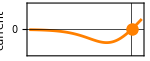

```mathematica
savePanels[{"Fig2Ai.svg"},roots=SolveValues[Simplify[3/5 Subscript[f, NMDA][mVto[u mV]]==0],u,Reals];Show[Plot[Evaluate[1/5 (-3) Subscript[f, NMDA][mVto[u mV]]],{u,-100,10},AspectRatio->1/((3 GoldenRatio)/2),Frame->True,FrameLabel->{{"current",None},{None,None}},FrameTicks->{{{0},None},{{{-90,None},{0,None}},None}},PlotRange->{{-100,10},{-0.35,0.35}},ImageSize->150,PlotStyle->RGBColor["#ff8000"],GridLines->{{0}},GridLinesStyle->Black],(Graphics[{RGBColor["#ff8000"],PointSize[0.06],Point[{#1,0}]}]&)/@roots]]
```

#### Fig. 2Aii

GIRK channels - voltage gating modeled with a sigmoid

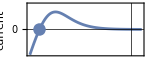

```mathematica
savePanels[{"Fig2Aii.svg"},roots=SolveValues[Simplify[7/5 Subscript[f, GIRK][mVto[u mV]]==0],u,Reals];Show[Plot[Evaluate[1/5 (-7) Subscript[f, GIRK][mVto[u mV]]],{u,-100,10},AspectRatio->1/((3 GoldenRatio)/2),Frame->True,FrameLabel->{{"current",None},{None,None}},FrameTicks->{{{0},None},{{{-90,None},{0,None}},None}},PlotRange->{{-100,10},{-0.35,0.35}},ImageSize->150,PlotStyle->RGBColor["#6580b1"],GridLines->{{0}},GridLinesStyle->Black],(Graphics[{RGBColor["#6580b1"],PointSize[0.06],Point[{#1,0}]}]&)/@roots]]
```

#### Fig. 2Aiii

Coactive NMDA and GIRK channels

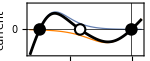

```mathematica
savePanels[{"Fig2Aiii.svg"},roots=SolveValues[Simplify[7/5 Subscript[f, GIRK][mVto[u mV]]+3/5 Subscript[f, NMDA][mVto[u mV]]==0],u,Reals];Show[Plot[Evaluate[{1/5 (-7) Subscript[f, GIRK][mVto[u mV]],1/5 (-3) Subscript[f, NMDA][mVto[u mV]],-(7/5 Subscript[f, GIRK][mVto[u mV]]+3/5 Subscript[f, NMDA][mVto[u mV]])}],{u,-100,10},AspectRatio->1/((3 GoldenRatio)/2),Frame->True,FrameLabel->{{"current",None},{None,None}},FrameTicks->{{{0},None},{None,None}},PlotRange->{{-100,10},{-0.35,0.35}},ImageSize->150,PlotStyle->{Directive[RGBColor["#6580b1"],Thickness[0.006]],Directive[RGBColor["#ff8000"],Thickness[0.006]],Black},GridLines->{{0}},GridLinesStyle->Black],(Graphics[{Black,PointSize[0.06],Point[{#1,0}]}]&)/@roots,(Graphics[{White,PointSize[0.04],Point[{#1,0}]}]&)/@roots⟦2;;All;;2⟧]]
```

#### Fig. 2Aiv

Coactive voltage-gated depolarizing and hyperpolarizing channels - approximated with a cubic polynomial

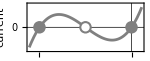

```mathematica
savePanels[{"Fig2Aiv.svg"},roots=SolveValues[Simplify[𝒻[mVto[u mV]]==0/.{𝓇->0}],u,Reals];Show[Plot[Evaluate[{-𝒻[mVto[u mV]]/.{𝓇->0}}],{u,-100,10},AspectRatio->1/((3 GoldenRatio)/2),Frame->True,FrameLabel->{{"current",None},{"voltage (mV)",None}},FrameTicks->{{{0},None},{{{-90,-90},{0,0}},None}},PlotRange->{{-100,10},{-0.35,0.35}},ImageSize->150,PlotStyle->{Gray},GridLines->{{0}},GridLinesStyle->Black],(Graphics[{Gray,PointSize[0.06],Point[{#1,0}]}]&)/@roots,(Graphics[{White,PointSize[0.04],Point[{#1,0}]}]&)/@roots⟦2;;All;;2⟧]]
```

### Fig. 3 IV curves:

Shows how localizing conductances to discrete synaptic sites changes the number of stable equilibria in the boundary segments. Neighbors are assumed to be at plateau (e_NMDA) and rest (e_GIRK).

#### Helper code to plot the IV curves

plotIVu1 plots the cubic membrane current and total current for a segment between resting and plateauing neighbors, marking the equilibria.

```mathematica
plotIVu1[repval_] :=
  Module[{roots},
    roots = SolveValues[Simplify[𝒻[mVto[u * mV]] + ℓ^2 * ((Subscript[e, NMDA] - mVto[u * mV]) / Δx^2)
       + ℓ^2 * ((Subscript[e, GIRK] - mVto[u * mV]) / Δx^2) == 0 /. repval], u, Reals];
    Show[Plot[Evaluate[{-𝒻[mVto[u * mV]] /. repval, -(𝒻[mVto[u * mV]] + ℓ^2 * ((Subscript[e, NMDA] - 
      mVto[u * mV]) / Δx^2) + ℓ^2 * ((Subscript[e, GIRK] - mVto[u * mV]) / Δx^2)) /. repval}], {u, -100, 10
      }, AspectRatio -> 1 / ((3/2) * GoldenRatio), Frame -> True, FrameLabel -> {{"current", None}, {"", None
      }}, FrameTicks -> {{{0}, None}, {{-90, 0}, None}}, PlotRange -> {{-100, 10}, {-0.35, 0.35}}, ImageSize
       -> 150, PlotStyle -> {Directive[Gray, Thickness[0.006]], Brown}, GridLines -> {{1}, {0}}, GridLinesStyle
       -> Black, Axes -> False], (Graphics[{Brown, PointSize[0.06], Point[{#1, 0}]}]&) /@ roots, (Graphics[
      {White, PointSize[0.04], Point[{#1, 0}]}]&) /@ roots[[2 ;; All ;; 2]]]
  ];
```

#### Fig. 3Aii

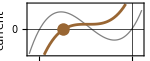

```mathematica
savePanels[{"Fig3Aii.svg"},repval={𝓇->(Subscript[G, NMDA]-Subscript[G, GIRK])/(Subscript[G, NMDA]+Subscript[G, GIRK])/.{Subscript[G, GIRK]->(4 Subscript[G, NMDA])/3},Δx->2 ℓ};Null;plotIVu1[repval]]
```

#### Fig. 3Bii

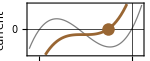

```mathematica
savePanels[{"Fig3Bii.svg"},repval={𝓇->(Subscript[G, NMDA]-Subscript[G, GIRK])/(Subscript[G, NMDA]+Subscript[G, GIRK])/.{Subscript[G, GIRK]->(3 Subscript[G, NMDA])/4},Δx->2 ℓ};Null;plotIVu1[repval]]
```

#### Fig. 3Cii

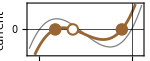

```mathematica
savePanels[{"Fig3Cii.svg"},repval={𝓇->(Subscript[G, NMDA]-Subscript[G, GIRK])/(Subscript[G, NMDA]+Subscript[G, GIRK])/.{Subscript[G, GIRK]->(3 Subscript[G, NMDA])/4},Δx->3 ℓ};Null;plotIVu1[repval]]
```

### Fig. 4 IV curves

Local current–voltage curves and stability at different synaptic spacings (Fig. 4).

#### Thevenin equivalent conductances: g_dis, g_prx

The Thevenin equivalent conductance G_∞ for a long dendrite with membrane conductance G_Ch

Solve for the input conductance of a semi-infinite chain of axially coupled compartments.

```mathematica
Subscript[𝒢, ∞soln]=Simplify[Solve[1/Subscript[G, ∞]==Subscript[R, s]+1/(Subscript[G, Ch]+Subscript[G, ∞]), Subscript[G, ∞]],{Subscript[G, Ch]>0}][[2]][[1]]
```

G_∞→1/2 (-G_Ch+(√(G_Ch (4+G_Ch R_s)))/(√R_s))

For the proximal side, with the dendrite mainly at rest and thus GIRK channels dominating (G_Ch=G_GIRK)

Evaluate the input conductance of the resting chain.

```mathematica
Subscript[G, prx]=FullSimplify[Subscript[G, ∞]/. Subscript[𝒢, ∞soln]/.{Subscript[G, Ch]-> Subscript[G, GIRK]},Subscript[R, s]>0]
```

1/2 (-G_GIRK+√(G_GIRK (G_GIRK+4/R_s)))

For the distal side, with the dendrite mainly at plateau and thus NMDA channels dominating (G_Ch=G_NMDA)

Evaluate the input conductance of the plateauing chain.

```mathematica
Subscript[G, dis]=FullSimplify[Subscript[G, ∞]/. Subscript[𝒢, ∞soln]/.{Subscript[G, Ch]-> Subscript[G, NMDA]},Subscript[R, s]>0]
```

1/2 (-G_NMDA+√(G_NMDA (G_NMDA+4/R_s)))

Converting from units of G_NMDA, G_GIRK, and R_s to units of (Δx/ℓ), G_c, and 𝓇=Δ𝒢_c/(2 𝒢_c).

Express NMDA and GIRK conductances in terms of their mean and normalized imbalance.

```mathematica
ChGtoGcr=Simplify@Solve[{Subscript[G, c]==(Subscript[G, NMDA]+Subscript[G, GIRK])/2,𝓇==(Subscript[G, NMDA]-Subscript[G, GIRK])/(Subscript[G, NMDA]+Subscript[G, GIRK])},{Subscript[G, NMDA],Subscript[G, GIRK]}][[1]]
```

{G_NMDA→(1+𝓇) G_c,G_GIRK→-((-1+𝓇) G_c)}

Express axial resistance in terms of synaptic spacing, electrotonic length and mean conductance.

```mathematica
Rstoℓr=Solve[1/(Subscript[R, s] Subscript[G, c])==(ℓ/Δx)^2,Subscript[R, s]][[1]]
```

{R_s→Δx^2/(ℓ^2 G_c)}

Normalizing by G_c

Normalize the input conductance of the resting chain.

```mathematica
Subscript[g, prx]=FullSimplify[Subscript[G, prx]/Subscript[G, c]/.ChGtoGcr/.Rstoℓr,Subscript[G, c]>0]
```

1/2 (-1+𝓇+√((-1+𝓇) (-1+𝓇-(4 ℓ^2)/Δx^2)))

Normalize the input conductance of the plateauing chain.

```mathematica
Subscript[g, dis]=FullSimplify[Subscript[G, dis]/Subscript[G, c]/.ChGtoGcr/.Rstoℓr,Subscript[G, c]>0]
```

1/2 (-1-𝓇+√((1+𝓇) (1+𝓇+(4 ℓ^2)/Δx^2)))

#### Helper code to plot the IV curves

plotIVu1Thev plots membrane and total currents for the segment nearer the plateau front, using the equivalent loads of the adjoining chains.

```mathematica
plotIVu1Thev[repval_]:=Module[{roots},
roots=SolveValues[Simplify[((1-𝓇)Subscript[f, GIRK][mVto[u mV]]+(1+𝓇)Subscript[f, NMDA][mVto[u mV]]+Subscript[g, dis](Subscript[e, NMDA]-mVto[u mV])+ℓ^2(Subscript[e, GIRK]-mVto[u mV])/Δx^2==0)/.repval],u,Reals];
Show[Plot[Evaluate[{
-((1-𝓇)Subscript[f, GIRK][mVto[u mV]]+(1+𝓇)Subscript[f, NMDA][mVto[u mV]])/.repval,
-((1-𝓇)Subscript[f, GIRK][mVto[u mV]]+(1+𝓇)Subscript[f, NMDA][mVto[u mV]]+Subscript[g, dis](Subscript[e, NMDA]-mVto[u mV])+ℓ^2(Subscript[e, GIRK]-mVto[u mV])/Δx^2
)/.repval
}],{u,-100,10},
AspectRatio->1/(3/2 GoldenRatio),Frame->True,FrameLabel->{{"current", None}, {"",None}},FrameTicks->{{{0},None},{{-90,0},None}},PlotRange->{{-100,10},{-0.4,0.4}},ImageSize->125,PlotStyle->{Directive[Black,Thickness[0.006]],Brown,Black},GridLines->{{0}},GridLinesStyle->Black],
Graphics[{Brown,PointSize[0.06],Point[{#,0}]}]&/@roots,
Graphics[{White,PointSize[0.04],Point[{#,0}]}]&/@roots[[2;;;;2]]
]
]
```

plotIVu2Thev plots membrane and total currents for the farther segment, using the equivalent loads of the adjoining chains.

```mathematica
plotIVu2Thev[repval_]:=Module[{roots},
roots=SolveValues[Simplify[((1-𝓇)Subscript[f, GIRK][mVto[u mV]]+(1+𝓇)Subscript[f, NMDA][mVto[u mV]]+ℓ^2(Subscript[e, GIRK]-mVto[u mV])/Δx^2+Subscript[g, prx](Subscript[e, GIRK]-mVto[u mV])==0)/.repval],u,Reals];
Show[Plot[Evaluate[{
-((1-𝓇)Subscript[f, GIRK][mVto[u mV]]+(1+𝓇)Subscript[f, NMDA][mVto[u mV]])/.repval,
-((1-𝓇)Subscript[f, GIRK][mVto[u mV]]+(1+𝓇)Subscript[f, NMDA][mVto[u mV]]+ℓ^2(Subscript[e, GIRK]-mVto[u mV])/Δx^2+Subscript[g, prx](Subscript[e, GIRK]-mVto[u mV])
)/.repval
}],{u,-100,10},
AspectRatio->1/(3/2 GoldenRatio),Frame->True,FrameLabel->{{"current", None}, {"",None}},FrameTicks->{{{0},None},{{-90,0},None}},PlotRange->{{-100,10},{-0.4,0.4}},ImageSize->125,PlotStyle->{Directive[Black,Thickness[0.006]],Purple,Black},GridLines->{{0}},GridLinesStyle->Black],
Graphics[{Purple,PointSize[0.06],Point[{#,0}]}]&/@roots,
Graphics[{White,PointSize[0.04],Point[{#,0}]}]&/@roots[[2;;;;2]]
]
]
```

#### Fig. 4Ai

```mathematica
savePanels[{"Fig4Ai.svg"},repval={𝓇->-6/10,Δx->2 ℓ};Null;plotIVu1Thev[repval]]
```

-Graphics-

#### Fig. 4Aii

```mathematica
savePanels[{"Fig4Aii.svg"},repval={𝓇->-6/10,Δx->2 ℓ};Null;plotIVu2Thev[repval]]
```

-Graphics-

#### Fig. 4Bi

```mathematica
savePanels[{"Fig4Bi.svg"},repval={𝓇->-4/10,Δx->2.5 ℓ};Null;plotIVu1Thev[repval]]
```

-Graphics-

#### Fig. 4Bii

```mathematica
savePanels[{"Fig4Bii.svg"},repval={𝓇->-4/10,Δx->2.5 ℓ};Null;plotIVu2Thev[repval]]
```

-Graphics-

#### Fig. 4Ci

```mathematica
savePanels[{"Fig4Ci.svg"},repval={𝓇->-3/10,Δx->4 ℓ};Null;plotIVu1Thev[repval]]
```

-Graphics-

#### Fig. 4Cii

```mathematica
savePanels[{"Fig4Cii.svg"},repval={𝓇->-3/10,Δx->4 ℓ};Null;plotIVu2Thev[repval]]
```

-Graphics-

## Channels distributed along a dendrite

#### Fig. 2Bi

```mathematica
savePanels[{"Fig2Bi.png"},repval={𝓇->(Subscript[G, NMDA]-Subscript[G, GIRK])/(Subscript[G, NMDA]+Subscript[G, GIRK])/.{Subscript[G, NMDA]->1 Subscript[G, GIRK]},Subscript[G, AMPA]->25 Subscript[𝒢, c] ℓ,τA->2,τ->1,ℓ->1};Null;uinit[x_]:=-1;Null;diffeq=Hold[τ D[u[x,t], t]==𝒻[u[x,t]]+ℓ^2 D[u[x,t], x,x]+(Subscript[G, AMPA] δ[0.1][x] Subscript[f, AMPA][u[x,t],t,τA,40])/(Subscript[𝒢, c] ℓ)];Null;ndsol=NDSolve[{ReleaseHold[diffeq],u[x,-20]==uinit[x],u[-30,t]==-1,u[30,t]==-1}//.repval,u[x,t],{x,-30,30},{t,-20,160},MaxStepSize->0.01];Null;Show[Plot3D[Evaluate[u[x,t]/.ndsol],{x,-15,15},{t,0,160},AxesLabel->{"","",""},Axes->True,PlotRange->All,PlotPoints->100,Mesh->{Range[-30,30,5],Range[-0.3,160,20]},ViewPoint->{0,-2,1},ViewVertical->{0,0,1},Ticks->{({#1,""}&)/@Range[-30,30,5],({#1,""}&)/@Range[0,160,20],{{-1,-90},{1,0}}},ImageSize->200,AxesEdge->{{-1,-1},{-1,1},{-1,-1}}],ListPointPlot3D[{{0,40,1}},PlotStyle->{Red,PointSize[0.02]}]]]
```

-Graphics3D-

#### Fig. 2Bii

```mathematica
savePanels[{"Fig2Bii.png"},repval={𝓇->(Subscript[G, NMDA]-Subscript[G, GIRK])/(Subscript[G, NMDA]+Subscript[G, GIRK])/.{Subscript[G, NMDA]->1 Subscript[G, GIRK]},Subscript[G, AMPA]->25 Subscript[𝒢, c] ℓ,Subscript[G, AMPA]->25 Subscript[𝒢, c] ℓ,τA->2,τ->1,ℓ->1};Null;uinit[x_]:=-1;Null;diffeq=Hold[τ D[u[x,t], t]==𝒻[u[x,t]]+ℓ^2 D[u[x,t], x,x]+(Subscript[G, AMPA] (δ[0.1][x]+δ[0.1][x+5]) Subscript[f, AMPA][u[x,t],t,τA,40])/(Subscript[𝒢, c] ℓ)];Null;ndsol=NDSolve[{ReleaseHold[diffeq],u[x,-20]==uinit[x],u[-30,t]==-1,u[30,t]==-1}//.repval,u[x,t],{x,-30,30},{t,-20,160},MaxStepSize->0.01];Null;Show[Plot3D[Evaluate[u[x,t]/.ndsol],{x,-15,15},{t,0,160},AxesLabel->{"","",""},Axes->True,PlotRange->All,PlotPoints->100,Mesh->{Range[-30,30,5],Range[-0.3,160,20]},ViewPoint->{0,-2,1},ViewVertical->{0,0,1},Ticks->{({#1,""}&)/@Range[-30,30,5],({#1,""}&)/@Range[0,160,20],{{-1,-90},{1,0}}},ImageSize->200,AxesEdge->{{-1,-1},{-1,1},{-1,-1}}],ListPointPlot3D[{{0,40,1},{-5,40,1}},PlotStyle->{Red,PointSize[0.02]}]]]
```

-Graphics3D-

#### Fig. 2Ci

```mathematica
savePanels[{"Fig2Ci.png"},repval={𝓇->(Subscript[G, NMDA]-Subscript[G, GIRK])/(Subscript[G, NMDA]+Subscript[G, GIRK])/.{Subscript[G, NMDA]->(3 Subscript[G, GIRK])/4}};Null;uinit[x_]:=-Tanh[(x-0.5)/(2 ℓ)];Null;diffeq=Hold[τ D[u[x,t], t]==𝒻[u[x,t]]+ℓ^2 D[u[x,t], x,x]];Null;ndsol=NDSolve[{ReleaseHold[diffeq],u[x,-20]==uinit[x],u[-30,t]==1,u[30,t]==-1}/.repval/.{ℓ->1,τ->1},u[x,t],{x,-30,30},{t,-20,160},MaxStepSize->0.01];Null;Show[Plot3D[Evaluate[u[x,t]/.ndsol],{x,-15,15},{t,0,160},AxesLabel->{"","",""},Axes->True,PlotRange->All,PlotPoints->100,Mesh->{Range[-15,15,5],Range[0,160,20]},ViewPoint->{0,-2,1},ViewVertical->{0,0,1},Ticks->{({#1,""}&)/@Join[Range[-5,-15,-5],Range[0,15,5]],({#1,""}&)/@Range[0,160,20],{{-1,""},{1,""}}},ImageSize->200,AxesEdge->{{-1,-1},{-1,1},{-1,-1}}]]]
```

-Graphics3D-

#### Fig. 2Cii

```mathematica
savePanels[{"Fig2Cii.png"},repval={𝓇->(Subscript[G, NMDA]-Subscript[G, GIRK])/(Subscript[G, NMDA]+Subscript[G, GIRK])/.{Subscript[G, NMDA]->1 Subscript[G, GIRK]}};Null;uinit[x_]:=-Tanh[(x-0.5)/(2 ℓ)];Null;diffeq=Hold[τ D[u[x,t], t]==𝒻[u[x,t]]+ℓ^2 D[u[x,t], x,x]];Null;ndsol=NDSolve[{ReleaseHold[diffeq],u[x,-20]==uinit[x],u[-30,t]==1,u[30,t]==-1}/.repval/.{ℓ->1,τ->1},u[x,t],{x,-30,30},{t,-20,160},MaxStepSize->0.01];Null;Show[Plot3D[Evaluate[u[x,t]/.ndsol],{x,-15,15},{t,0,160},AxesLabel->{"","",""},Axes->True,PlotRange->All,PlotPoints->100,Mesh->{Range[-15,15,5],Range[0,160,20]},ViewPoint->{0,-2,1},ViewVertical->{0,0,1},Ticks->{({#1,""}&)/@Join[Range[-5,-15,-5],Range[0,15,5]],({#1,""}&)/@Range[0,160,20],{{-1,""},{1,""}}},ImageSize->200,AxesEdge->{{-1,-1},{-1,1},{-1,-1}}]]]
```

-Graphics3D-

## Channels localized to synapses

### Channels modeled with a cubic

Front drift and anchoring with the cubic current (Fig. 3A–D).

#### Simulating dendrite voltage with channels modelled with a cubic

checkDriftCubic evolves a front in the discrete cubic model and classifies it as advancing, retreating or anchored. Its local uinit function sets the initial voltage profile.

```mathematica
checkDriftCubic[repval_, plot_:False, offset_:0] :=
  Module[{nN, xs, vars, uinit, eqs, tlim, ndsol},
    nN =
      If[((Δx / ℓ) ^ 2 //. repval) > 4,
        10
        ,
        20
      ];
    xs = Range[-nN, nN];
    vars = Table[u[i][t], {i, -nN, nN}];
    uinit[x_] := -Tanh[(x + offset) / (2 * ℓ)];
    eqs =
      Table[
        τ * Derivative[1][u[i]][t] ==
          𝒻[u[i][t]] +
            (ℓ / Δx) ^ 2 *
              (
                (
                    If[i < nN,
                        u[i + 1][t]
                        ,
                        u[i][t]
                      ] +
                      If[i > -nN,
                        u[i - 1][t]
                        ,
                        u[i][t]
                      ]
                  ) - 2 * u[i][t]
              )
        ,
        {i, -nN, nN}
      ];
    tlim = 50;
    ndsol = NDSolve[Flatten[{eqs, Table[u[i][-20] == uinit[xs[[i + nN + 1]] * Δx], {i, -nN, nN}]}] //.
       repval, vars, {t, -20, tlim}, MaxStepSize -> 0.1];
    If[plot,
      Print[Show[ListPlot3D[Flatten[Table[{xs[[i + nN + 1]], t, (u[i][t] /. ndsol)[[1]]}, {i, -2, 2},
         {t, 0, tlim, 1}], 1], Mesh -> {Range[-nN, nN, 1], Range[0, tlim, 10]}, PlotRange -> {{-2, 2}, All, {
        -1.01, 1.01}}, AxesLabel -> None, ViewPoint -> {0, -2, 1}, ViewVertical -> {0, 0, 1}, Axes -> True, ImageSize
         -> 200, Ticks -> {({#1, ""}&) /@ Range[-nN, nN, 1], ({#1, ""}&) /@ Range[0, tlim, 10], {{-1, ""}, {1,
         ""}}}]]]
    ];
    If[(u[-nN][t] /. ndsol /. {t -> tlim})[[1]] < 0,
      Return[r]
    ];
    If[(u[nN][t] /. ndsol /. {t -> tlim})[[1]] > 0,
      Return[p]
    ];
    rmax = MaximalBy[Evaluate[Table[(u[i][t] /. ndsol /. {t -> tlim})[[1]], {i, -nN, nN}]] - Evaluate[
      Table[(u[i][t] /. ndsol /. {t -> 0.75 * tlim})[[1]], {i, -nN, nN}]], Abs][[1]];
    If[rmax > 0.1,
      p
      ,
      If[rmax < -0.1,
        r
        ,
        s
      ]
    ]
  ];
```

#### Fig. 3Ai: Boundary drift - plateau retreats

```mathematica
savePanels[{"Fig3Ai.png"},repval={𝓇->(Subscript[G, NMDA]-Subscript[G, GIRK])/(Subscript[G, NMDA]+Subscript[G, GIRK])/.{Subscript[G, GIRK]->(4 Subscript[G, NMDA])/3},Δx->2 ℓ,τ->1};Null;checkDriftCubic[repval,True,-3 ℓ]]
```

-Graphics3D-

r

#### Fig. 3Bi: Boundary drift - plateau advances

```mathematica
savePanels[{"Fig3Bi.png"},repval={𝓇->(Subscript[G, NMDA]-Subscript[G, GIRK])/(Subscript[G, NMDA]+Subscript[G, GIRK])/.{Subscript[G, GIRK]->(3 Subscript[G, NMDA])/4},Δx->2 ℓ,τ->1};Null;checkDriftCubic[repval,True,3 ℓ]]
```

-Graphics3D-

p

#### Fig. 3Ci: Boundary anchored

```mathematica
savePanels[{"Fig3Ci.png"},repval={𝓇->(Subscript[G, NMDA]-Subscript[G, GIRK])/(Subscript[G, NMDA]+Subscript[G, GIRK])/.{Subscript[G, GIRK]->(3 Subscript[G, NMDA])/4},Δx->3 ℓ,τ->1};Null;checkDriftCubic[repval,True,1 ℓ]]
```

-Graphics3D-

s

#### Fig. 3D: Sweeping parameters - voltage gating modeled as a cubic

Sweep spacing and conductance imbalance to map front anchoring in the cubic model.

```mathematica
{vals3o,coords3o}=theCut[checkDriftCubic[{Δx->√#1 ℓ,𝓇->#2,τ->0.01},False,0.5 Δx]&,{{RsGc,0.1,20},{𝓇,-1,1}},4,8,{p,r,s}];boundaryPlot=plotCutBoundary2d[{vals3o,coords3o},{{RsGc,0.1,20},{𝓇,-1,1}},{p,r,s},{White,White,LightGray},{Dotted,Thick}];
```

2

3

4

5

6

7

8

Plot the front-anchoring boundaries against spacing and conductance imbalance.

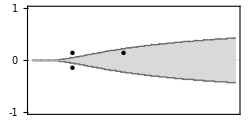

```mathematica
savePanels[{"Fig3D.png"},ticksSqrt=Table[{i^2,If[Mod[i,1]==0,IntegerPart[i],""],If[Mod[i,1]==0,0.02,0.01]},{i,0,10,0.1}];ticksBase=Table[{i,If[Mod[i,10]==0,IntegerPart[i],""],If[Mod[i,10]==0,0.02,0.02/3]},{i,0,40,1}];ticksBaseSlnt=Table[{i,"",If[Mod[i,10]==0,0.02,0.02/3]},{i,0,40,1}];Show[boundaryPlot,ListPlot[{{4,1/7},{9,1/7},{4,-1/7}},PlotStyle->Black],GridLines->{{},{0}},Method->{"GridLinesInFront"->True},GridLinesStyle->{Gray},FrameTicks->{{{-1,0,1},None},{ticksBaseSlnt,ticksSqrt}},ImageSize->250,AspectRatio->1/2,FrameLabel->{"",""},PlotRange->{{0,20},{-1,1}},Frame->True,PlotRangePadding->0]]
```

### Channels modeled with a sigmoid

Front anchoring with sigmoid-gated NMDA and GIRK currents (Fig. 3E,F).

#### Simulating dendrite voltage with channels modelled with a sigmoid

Simulates a dendrite with NMDA and GIRK channels localized to synapses (when m is 1), or with GIRK channels distributed to m compartments between localized NMDA synapses.

checkDriftSig evolves a front with sigmoid-gated NMDA and GIRK currents and classifies its drift. m sets the shaft subdivisions per synaptic interval; uinit sets the initial voltage profile.

```mathematica
checkDriftSig[repval_, m_, offset_:0] :=
  Module[{nN, nm, xs, vars, uinit, eqs, tlim, ndsol, rmax},
    nN =
      If[((Δx / ℓ) ^ 2 //. repval) > 4,
        10
        ,
        20
      ];
    nm = nN * m + Floor[m / 2];
    xs = Range[-nm, nm];
    vars = Table[u[i][t], {i, -nm, nm}];
    uinit[x_] := -(2 * UnitStep[(x + offset) / (2 * ℓ)] - 1);
    eqs =
      Table[
        τ * Derivative[1][u[i]][t] ==
          If[Mod[i, m] == 0,
              m * (1 + 𝓇) * Subscript[f, NMDA][u[i][t]]
              ,
              0
            ] + (1 - 𝓇) * Subscript[f, GIRK][u[i][t]] +
            m^2 * (ℓ / Δx) ^ 2 *
              (
                If[i < nm,
                    u[i + 1][t]
                    ,
                    u[i][t]
                  ] +
                  If[i > -nm,
                    u[i - 1][t]
                    ,
                    u[i][t]
                  ] - 2 * u[i][t]
              )
        ,
        {i, -nm, nm}
      ];
    tlim = 50;
    ndsol = NDSolve[Flatten[{eqs, Table[u[i][-20] == uinit[(xs[[i + nm + 1]] * Δx) / m], {i, -nm, nm}
      ]}] //. repval, vars, {t, -20, tlim}, MaxStepSize -> 0.1];
    If[(u[-nm][t] /. ndsol /. {t -> tlim})[[1]] < 0,
      Return[r]
    ];
    If[(u[nm][t] /. ndsol /. {t -> tlim})[[1]] > 0,
      Return[p]
    ];
    rmax = MaximalBy[Evaluate[Table[(u[i][t] /. ndsol /. {t -> tlim})[[1]], {i, -nm, nm}]] - Evaluate[
      Table[(u[i][t] /. ndsol /. {t -> 0.75 * tlim})[[1]], {i, -nm, nm}]], Abs][[1]];
    If[rmax > 0.1,
      p
      ,
      If[rmax < -0.1,
        r
        ,
        s
      ]
    ]
  ];
```

NMDA and GIRK channels localized to synapses:

NMDA channels localized to synapses with GIRK channels distributed to m=10 compartments between each pair.

#### Fig. 3E: Sweeping parameters - NMDA and GIRK channels modeled with a sigmoid

Map front anchoring with NMDA and GIRK channels localized to synaptic sites.

```mathematica
{vals3o,coords3o}=theCut[checkDriftSig[{Δx->√#1 ℓ,𝓇->#2,τ->0.01},1,0.5 Δx]&,{{RsGc,0.1,20},{𝓇,-1,1}},4,8,{p,r,s}];boundaryPlot=plotCutBoundary2d[{vals3o,coords3o},{{RsGc,0.1,20},{𝓇,-1,1}},{p,r,s},{White,White,LightGray},{Dotted,Thick}];
```

2

3

4

5

6

7

8

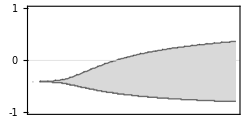

```mathematica
savePanels[{"Fig3E.png"},ticksSqrt=Table[{i^2,If[Mod[i,1]==0,IntegerPart[i],""],If[Mod[i,1]==0,0.02,0.01]},{i,0,10,0.1}];ticksSqrtSlnt=Table[{i^2,"",If[Mod[i,1]==0,0.02,0.01]},{i,0,10,0.1}];ticksBase=Table[{i,If[Mod[i,10]==0,IntegerPart[i],""],If[Mod[i,10]==0,0.02,0.02/3]},{i,0,40,1}];ticksBaseSlnt=Table[{i,"",If[Mod[i,10]==0,0.02,0.02/3]},{i,0,40,1}];Show[boundaryPlot,PlotStyle->Black,GridLines->{{},{0}},Method->{"GridLinesInFront"->True},GridLinesStyle->{Gray},FrameTicks->{{{-1,0,1},None},{ticksBaseSlnt,ticksSqrtSlnt}},ImageSize->250,AspectRatio->1/2,FrameLabel->{"",""},PlotRange->{{0,20},{-1,1}},Frame->True,PlotRangePadding->0]]
```

#### Fig. 3F: Sweeping parameters - GIRK channels distributed along the dendrite

Map front anchoring with synaptic NMDA channels and shaft-distributed GIRK channels.

```mathematica
{vals3o,coords3o}=theCut[checkDriftSig[{Δx->√#1 ℓ,𝓇->#2,τ->0.01},10,0.5 Δx]&,{{RsGc,0.1,20},{𝓇,-1,1}},4,8,{p,r,s}];boundaryPlot=plotCutBoundary2d[{vals3o,coords3o},{{RsGc,0.1,20},{𝓇,-1,1}},{p,r,s},{White,White,LightGray},{Dotted,Thick}];
```

2

3

4

5

6

7

8

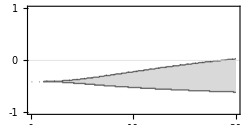

```mathematica
savePanels[{"Fig3F.png"},ticksSqrt=Table[{i^2,If[Mod[i,1]==0&&i≠1,IntegerPart[i],""],If[Mod[i,1]==0,0.02,0.01]},{i,0,10,0.1}];ticksSqrtSlnt=Table[{i^2,"",If[Mod[i,1]==0,0.02,0.01]},{i,0,10,0.1}];Show[boundaryPlot,GridLines->{{},{0}},Method->{"GridLinesInFront"->True},GridLinesStyle->{Gray},FrameTicks->{{{-1,0,1},None},{{0,10,20},ticksSqrtSlnt}},ImageSize->250,FrameLabel->{"",""},Frame->True,PlotRangePadding->0,ImageSize->250,AspectRatio->1/2]]
```

### AMPA inputs advancing the plateau

AMPA inputs advancing or stalling an anchored front.

#### Simulating dendrite voltage with channels modelled with a sigmoid with AMPA inputs

checkAdvanceSig takes input times and model parameters, delivers transient AMPA inputs ahead of a front and tests if the front advances. uinit sets the initial voltage profile; the plot option displays its evolution.

```mathematica
checkAdvanceSig[𝒯_][repval_, m_, plot_:False, offset_:0, redDotHeight_:1] :=
  Module[{n, nN, nm, rnm, xs, vars, uinit, eqs, tlim, ndsol, redDotHeightv},
    n = Length[𝒯];
    nN =
      If[((Δx / ℓ) ^ 2 /. repval) > 4,
        10
        ,
        20
      ];
    nm = nN * m + Floor[m / 2];
    rnm = n * m + nm;
    xs = Range[-nm, rnm];
    vars = Table[u[i][t], {i, -nm, rnm}];
    uinit[x_] := -(2 * UnitStep[(x + offset) / (2 * ℓ)] - 1);
    eqs =
      Table[
        τ * Derivative[1][u[i]][t] ==
          If[Mod[i, m] == 0,
              m *
                (
                  (1 + 𝓇) * Subscript[f, NMDA][u[i][t]] +
                    If[1 <= i / m <= n,
                      (Subscript[G, AMPA] / Subscript[G, c]) * Subscript[f, AMPA][u[i][t], t, τA, 𝒯[[
                        i / m]]]
                      ,
                      0
                    ]
                )
              ,
              0
            ] + (1 - 𝓇) * Subscript[f, GIRK][u[i][t]] +
            m^2 * (ℓ / Δx) ^ 2 *
              (
                If[i < rnm,
                    u[i + 1][t]
                    ,
                    u[i][t]
                  ] +
                  If[i > -nm,
                    u[i - 1][t]
                    ,
                    u[i][t]
                  ] - 2 * u[i][t]
              )
        ,
        {i, -nm, rnm}
      ];
    tlim =
      Max[𝒯] +
        If[n > 1,
          2 * Abs[𝒯[[2]] - 𝒯[[1]]]
          ,
          20
        ];
    ndsol = NDSolve[Flatten[{eqs, Table[u[i][-20] == uinit[xs[[i + nm + 1]] * (Δx / m)], {i, -nm, rnm
      }]}] //. repval, vars, {t, -20, tlim}];
    If[plot,
      redDotHeightv = redDotHeight;
      If[redDotHeight == 1,
        redDotHeightv = {1, 1}
      ];
      Null;
      Print[Show[ListPlot3D[Flatten[Table[{xs[[i + nm + 1]], t, (u[i][t] /. ndsol)[[1]]}, {i, -(m + Floor[
        m / 2]), n * m + 2 * m + Floor[m / 2]}, {t, 0, tlim, τ /. repval}], 1], Mesh -> {Range[-m, n * m + 2 
        * m, m], Range[0, tlim, Abs[𝒯[[2]] - 𝒯[[1]]]]}, PlotRange -> {{-m, n * m + 2 * m}, All, {-1.01, 1.01}
        }, AxesLabel -> None, ViewPoint -> {0, -2, 1}, ViewVertical -> {0, 0, 1}, Axes -> True, ImageSize -> 
        200, Ticks -> {({#1, ""}&) /@ Range[-2, 5, 1], ({#1, ""}&) /@ Range[0, 120, 40], {{-1, ""}, {1, ""}}},
         AxesEdge -> {{-1, -1}, {-1, 1}, {-1, -1}}], ListPointPlot3D[Table[{i, 𝒯[[i]] + 2 * τA /. repval, redDotHeightv
        [[i]]}, {i, Range[Length[𝒯]]}], PlotStyle -> {Red, PointSize[0.02]}]]]
    ];
    If[(u[-nm][t] /. ndsol /. {t -> tlim})[[1]] < 0,
      Return[False]
    ];
    If[(u[nm][t] /. ndsol /. {t -> tlim})[[1]] > 0,
      Return[True]
    ];
    (u[n * m][t] /. ndsol /. {t -> tlim})[[1]] > (1/10) * (9 * (u[0][t] /. ndsol /. {t -> Min[𝒯] - 1}
      )[[1]] + 1 * (u[m][t] /. ndsol /. {t -> Min[𝒯] - 1})[[1]])
  ];
```

#### Fig. 5Ai

```mathematica
savePanels[{"Fig5Ai.png"},repval={𝓇->-0.4,Δx->2.5 ℓ,Subscript[G, AMPA]->0.2 Subscript[G, c],τA->2,τ->1};Null;checkAdvanceSig[{40,80}][repval,1,True,-0.5 Δx,{0.7,0.7}]]
```

{0.7,0.7}

-Graphics3D-

True

#### Fig. 5Aiii

```mathematica
savePanels[{"Fig5Aiii.png"},repval={𝓇->-0.4,Δx->2.5 ℓ,Subscript[G, AMPA]->0.2 Subscript[G, c],τA->2,τ->1};Null;checkAdvanceSig[{80,40}][repval,1,True,-0.5 Δx,{0.7,-0.6}]]
```

{0.7,-0.6}

-Graphics3D-

False

#### Fig. 5Bi

```mathematica
savePanels[{"Fig5Bi.png"},repval={𝓇->-0.4,Δx->2.5 ℓ,Subscript[G, AMPA]->0.375 Subscript[G, c],τA->2,τ->1};Null;checkAdvanceSig[{80,40}][repval,1,True,-0.5 Δx,{0.8,0.}]]
```

{0.8,0.}

-Graphics3D-

False

#### Fig. 5Biii

```mathematica
savePanels[{"Fig5Biii.png"},repval={𝓇->-0.4,Δx->2.5 ℓ,Subscript[G, AMPA]->0.5 Subscript[G, c],τA->2,τ->1};Null;checkAdvanceSig[{80,40}][repval,1,True,-0.5 Δx,{1,0.5}]]
```

{1,0.5}

-Graphics3D-

True

#### Fig. 5Ci

```mathematica
savePanels[{"Fig5Ci.png"},repval={𝓇->-0.6,Δx->3.5 ℓ,Subscript[G, AMPA]->0.3 Subscript[G, c],τA->2,τ->1};Null;checkAdvanceSig[{80,40}][repval,1,True,-0.5 Δx,{0.8,-0.4}]]
```

{0.8,-0.4}

-Graphics3D-

False

#### Fig. 5Ciii

```mathematica
savePanels[{"Fig5Ciii.png"},repval={𝓇->-0.6,Δx->3.5 ℓ,Subscript[G, AMPA]->3 Subscript[G, c],τA->2,τ->1};Null;checkAdvanceSig[{80,40}][repval,1,True,-0.5 Δx,{0.97,0.9}]]
```

{0.97,0.9}

-Graphics3D-

False

#### Fig. 5Di

```mathematica
savePanels[{"Fig5Di.png"},repval={𝓇->-0.3,Δx->4 ℓ,Subscript[G, AMPA]->0.2 Subscript[G, c],τA->2,τ->1};Null;checkAdvanceSig[{80,40}][repval,1,True,-0.5 Δx,{0.9,-0.55}]]
```

{0.9,-0.55}

-Graphics3D-

False

#### Fig. 5Diii

```mathematica
savePanels[{"Fig5Diii.png"},repval={𝓇->-0.3,Δx->4 ℓ,Subscript[G, AMPA]->0.5 Subscript[G, c],τA->2,τ->1};Null;checkAdvanceSig[{80,40}][repval,1,True,-0.5 Δx,{1,0.8}]]
```

{1,0.8}

-Graphics3D-

True

## Phase Portraits

phasePortraits plots the equilibria, separatrices and input-driven trajectories of the two segments ahead of the front.

```mathematica
phasePortraits[𝒯_][repval_, plotInputs_:True] :=
  Module[{urangex, urangey, rhs1, rhs2, rawSols, pts, uniquePts, sols, J, nc, ptsGraphics, fieldPlot,
     sepPts, sepPlot, eq1, eq2, solns, pp1, pp2, 𝒯v},
    urangex = {-1.3, 1.3};
    urangey = {-1.3, 1.3};
    rhs1 = (1 + 𝓇) * Subscript[f, NMDA][u[1][t]] + (1 - 𝓇) * Subscript[f, GIRK][u[1][t]] + Subscript[
      g, dis] * (Subscript[e, NMDA] - u[1][t]) + (ℓ / Δx) ^ 2 * (u[2][t] - u[1][t]);
    rhs2 = (1 + 𝓇) * Subscript[f, NMDA][u[2][t]] + (1 - 𝓇) * Subscript[f, GIRK][u[2][t]] + (ℓ / Δx) ^
       2 * (u[1][t] - u[2][t]) + Subscript[g, prx] * (Subscript[e, GIRK] - u[2][t]);
    rawSols = Quiet[(FindRoot[Evaluate[{rhs1 == 0, rhs2 == 0} /. repval], {{u[1][t], #1[[1]]}, {u[2][
      t], #1[[2]]}}]&) /@ Flatten[Table[{i, j}, {i, -1, 1, 1}, {j, -1, 1, 1}], 1]];
    rawSols = Select[rawSols, rhs1^2 + rhs2^2 < 0.0001 /. repval /. #1&];
    pts = N[{u[1][t], u[2][t]} /. rawSols];
    uniquePts = DeleteDuplicates[pts, EuclideanDistance[#1, #2] < 0.1&];
    sols = (Thread[{u[1][t], u[2][t]} -> #1]&) /@ uniquePts;
    J = D[{rhs1, rhs2}, {{u[1][t], u[2][t]}}];
    nc = ContourPlot[Evaluate[{rhs2 == 0, rhs1 == 0} /. repval], {u[2][t], urangex[[1]], urangex[[2]]
      }, {u[1][t], urangey[[1]], urangey[[2]]}, ContourStyle -> {Directive[Lighter[Purple], Thickness[0.004
      ]], Directive[Lighter[Brown], Thickness[0.004]]}];
    ptsGraphics =
      Graphics[
        Table[
          Module[{pt = {u[2][t], u[1][t]} /. sol, Jpt, evals},
            Jpt = J /. {u[2][t] -> pt[[1]], u[1][t] -> pt[[2]]} /. repval;
            evals = Eigenvalues[Jpt];
            If[AllTrue[evals, #1 < 0&],
              {Black, PointSize[Large], Point[pt]}
              ,
              {Black, PointSize[Large], Point[pt], White, PointSize[Medium], Point[pt]}
            ]
          ]
          ,
          {sol, sols}
        ]
      ];
    fieldPlot = StreamPlot[Evaluate[{rhs2, rhs1} /. repval], {u[2][t], urangex[[1]], urangex[[2]]}, {
      u[1][t], urangey[[1]], urangey[[2]]}, StreamStyle -> LightGray, StreamColorFunction -> None, StreamScale
       -> 0.25, StreamPoints -> 75];
    sepPts =
      Module[{tol = 10 ^ (-8), eps = 0.2, saddles, classifyPt},
        classifyPt[sol_] :=
          Module[{pt, Jpt, evals, evecs, pos, neg, vs},
            pt = N[{u[1][t], u[2][t]} /. sol];
            Jpt = N[J /. Thread[{u[1][t], u[2][t]} -> pt] /. repval];
            {evals, evecs} = Eigensystem[Jpt];
            pos = Flatten[Position[evals, _ ? (Re[#1] > tol&)]];
            neg = Flatten[Position[evals, _ ? (Re[#1] < -tol&)]];
            If[Length[pos] == 1 && Length[neg] == 1,
              vs = Normalize[evecs[[neg[[1]]]]];
              {pt + eps * vs, pt - eps * vs}
              ,
              Nothing
            ]
          ];
        saddles = Flatten[classifyPt /@ sols, 1];
        saddles = ({#1[[2]], #1[[1]]}&) /@ saddles;
        DeleteDuplicates[saddles, EuclideanDistance[#1, #2] < 10 ^ (-5)&]
      ];
    sepPlot = StreamPlot[Evaluate[{rhs2, rhs1} /. repval], {u[2][t], urangex[[1]], urangex[[2]]}, {u[
      1][t], urangey[[1]], urangey[[2]]}, StreamPoints -> {sepPts}, StreamStyle -> Directive[Cyan, Thickness[
      0.006]], StreamColorFunction -> None, StreamScale -> None, PlotRange -> {urangex, urangey}];
    If[!plotInputs,
      Print[Show[fieldPlot, sepPlot, nc, ptsGraphics, PlotRange -> All, Frame -> True, FrameLabel -> 
        {{"\!\(\*SubscriptBox[\(u\), \(1\)]\)", None}, {"\!\(\*SubscriptBox[\(u\), \(2\)]\)", None}}, FrameTicks
         -> {{{{-1, -90}, {1, 0}}, None}, {{{-1, -90}, {1, 0}}, None}}, ImageSize -> 150]];
      Return[Null]
    ];
    𝒯v = 𝒯;
    eq1 = (τ * D[u[1][t], t] == rhs1 + (Subscript[G, AMPA] / Subscript[G, c]) * Subscript[f, AMPA][u[
      1][t], t, τA, 𝒯v[[1]]]);
    eq2 = (τ * D[u[2][t], t] == rhs2 + (Subscript[G, AMPA] / Subscript[G, c]) * Subscript[f, AMPA][u[
      2][t], t, τA, 𝒯v[[2]]]);
    solns = NDSolve[{eq1, eq2, u[1][0] == -1, u[2][0] == -1} //. repval, {u[1], u[2]}, {t, 0, Max[𝒯v]
       + Min[𝒯v]}];
    pp1 = ParametricPlot[{u[2][t], u[1][t]} /. solns, {t, 𝒯v[[1]], 𝒯v[[1]] + Abs[𝒯v[[1]] - 𝒯v[[2]]]},
       PlotRange -> {{urangex[[1]], urangex[[2]]}, {urangey[[1]], urangey[[2]]}}, PlotStyle -> Directive[Thickness[
      0.008], Brown]];
    pp2 = ParametricPlot[{u[2][t], u[1][t]} /. solns, {t, 𝒯v[[2]], 𝒯v[[2]] + Abs[𝒯v[[1]] - 𝒯v[[2]]]},
       PlotRange -> {{urangex[[1]], urangex[[2]]}, {urangey[[1]], urangey[[2]]}}, PlotStyle -> Directive[Thickness[
      0.008], Purple]];
    Print[Show[fieldPlot, sepPlot, nc, pp1 /. Line[x_] :> {Arrowheads[{0., 0.08, 0, 0.08, 0.}], Arrow[
      x]}, pp2 /. Line[x_] :> {Arrowheads[{0., 0.08, 0, 0.08, 0.}], Arrow[x]}, ptsGraphics, PlotRange -> All,
       Frame -> True, FrameLabel -> {{"\!\(\*SubscriptBox[\(u\), \(1\)]\)", None}, {"\!\(\*SubscriptBox[\(u\), \(2\)]\)",
       None}}, FrameTicks -> {{{{-1, -90}, {1, 0}}, None}, {{{-1, -90}, {1, 0}}, None}}, ImageSize -> 150]]
      ;
  ];
```

#### Fig. 4Aiii

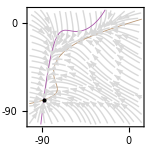

```mathematica
savePanels[{"Fig4Aiii.svg"},repval={𝓇->-0.6,Δx->2 ℓ,Subscript[G, AMPA]->0.4 Subscript[G, c],τA->2,τ->1};Null;phasePortraits[{40,80}][repval,False]]
```

#### Fig. 4Biii and Fig. 5Aii

In-order inputs, AMPA conductance in order-selective range

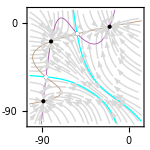

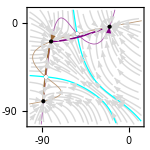

```mathematica
savePanels[{"Fig4Biii.svg","Fig5Aii.svg"},repval={𝓇->-0.4,Δx->2.5 ℓ,Subscript[G, AMPA]->0.2 Subscript[G, c],τA->2,τ->1};phasePortraits[{40,80}][repval,False];phasePortraits[{40,80}][repval]]
```

#### Fig. 5Aiv

Out-of-order inputs, AMPA conductance in order-selective range

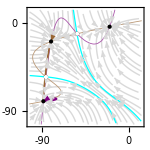

```mathematica
savePanels[{"Fig5Aiv.svg"},repval={𝓇->-0.4,Δx->2.5 ℓ,Subscript[G, AMPA]->0.2 Subscript[G, c],τA->2,τ->1};Null;phasePortraits[{80,40}][repval]]
```

#### Fig. 5Bii

Out-of-order inputs, higher AMPA conductance crosses near separatrix

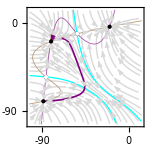

```mathematica
savePanels[{"Fig5Bii.svg"},repval={𝓇->-0.4,Δx->2.5 ℓ,Subscript[G, AMPA]->0.375 Subscript[G, c],τA->2,τ->1};Null;phasePortraits[{80,40}][repval]]
```

#### Fig. 5Biv

Out-of-order input crosses the near and far separatrices.

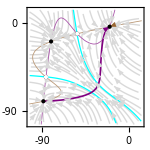

```mathematica
savePanels[{"Fig5Biv.svg"},repval={𝓇->-0.4,Δx->2.5 ℓ,Subscript[G, AMPA]->0.5 Subscript[G, c],τA->2,τ->1};Null;phasePortraits[{80,40}][repval]]
```

#### Fig. 5Cii

Out-of-order input remains in the rest-rest basin.

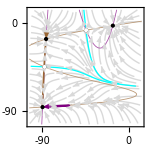

```mathematica
savePanels[{"Fig5Cii.svg"},repval={𝓇->-0.6,Δx->3.5 ℓ,Subscript[G, AMPA]->0.3 Subscript[G, c],τA->2,τ->1};Null;phasePortraits[{80,40}][repval]]
```

#### Fig. 5Civ

A tenfold AMPA increase leaves the out-of-order input in the rest-rest basin.

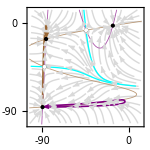

```mathematica
savePanels[{"Fig5Civ.svg"},repval={𝓇->-0.6,Δx->3.5 ℓ,Subscript[G, AMPA]->3 Subscript[G, c],τA->2,τ->1};Null;phasePortraits[{80,40}][repval]]
```

#### Fig. 4Ciii and 5Dii

Out-of-order inputs, AMPA conductance in order-selective range

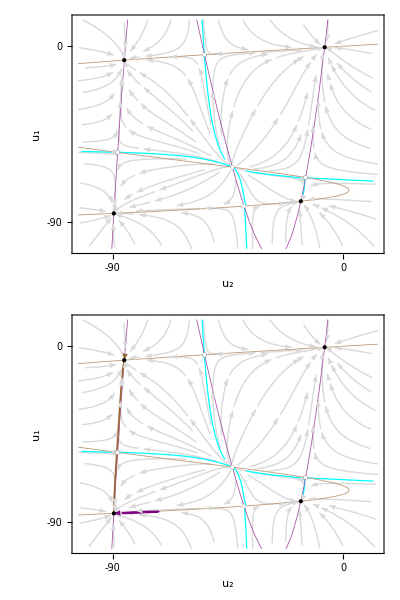

```mathematica
savePanels[{"Fig4Ciii.svg","Fig5Dii.svg"},repval={𝓇->-0.3,Δx->4 ℓ,Subscript[G, AMPA]->0.2 Subscript[G, c],τA->2,τ->1};phasePortraits[{80,40}][repval,False];phasePortraits[{80,40}][repval]]
```

#### Fig. 5Div

Out-of-order inputs, high AMPA conductance crosses separatrix between rest-rest and rest-plateau

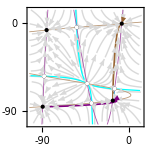

```mathematica
savePanels[{"Fig5Div.svg"},repval={𝓇->-0.3,Δx->4 ℓ,Subscript[G, AMPA]->0.5 Subscript[G, c],τA->2,τ->1};Null;phasePortraits[{80,40}][repval]]
```

## Counting stable points

countStable counts distinct stable states reached from different initial voltages in the two segments. solveOnce evolves one voltage pair after release from clamping; uinit sets the surrounding voltage profile.

```mathematica
countStable[repval_, m_, offset_ : -0.5 * Δx] :=
  Module[{nN, nm, xs, vars, uinit, eqs, tlim, holdTime, solveOnce, vcPairs, results, uniq, tol},
    nN =
      If[((Δx / ℓ) ^ 2 //. repval) > 4,
        10
        ,
        20
      ];
    nm = nN * m + Floor[m / 2];
    xs = Range[-nm, nm];
    vars = Table[u[i][t], {i, -nm, nm}];
    uinit[x_] := -Tanh[(x + offset) / (2 * ℓ)];
    tlim = 50;
    holdTime = tlim / 2;
    eqs =
      Table[
        τ * Derivative[1][u[i]][t] ==
          If[Mod[i, m] == 0,
              UnitStep[t - holdTime]
              ,
              1
            ] *
            (
              If[Mod[i, m] == 0,
                  m * (1 + 𝓇) * Subscript[f, NMDA][u[i][t]]
                  ,
                  0
                ] + (1 - 𝓇) * Subscript[f, GIRK][u[i][t]] +
                m^2 * (ℓ / Δx) ^ 2 *
                  (
                    If[i < nm,
                        u[i + 1][t]
                        ,
                        u[i][t]
                      ] +
                      If[i > -nm,
                        u[i - 1][t]
                        ,
                        u[i][t]
                      ] - 2 * u[i][t]
                  )
            )
        ,
        {i, -nm, nm}
      ];
    solveOnce[{vc1_, vc2_}] :=
      Module[{ndsol},
        ndsol =
          NDSolve[
            Flatten[
                {
                  eqs
                  ,
                  Table[
                    Switch[i,
                      m,
                        u[i][-20] == vc1
                      ,
                      2 * m,
                        u[i][-20] == vc2
                      ,
                      _,
                        u[i][-20] == uinit[(xs[[i + nm + 1]] * Δx) / m]
                    ]
                    ,
                    {i, -nm, nm}
                  ]
                }
              ] //. repval
            ,
            vars
            ,
            {t, -20, tlim}
          ];
        ndsol
      ];
    vcPairs = Tuples[{-0.8, 0.8}, 2];
    results =
      Table[
        With[{sol = solveOnce[pair]},
          Evaluate[{(u[m][t] /. sol)[[1]], (u[2 * m][t] /. sol)[[1]]}] /. t -> tlim
        ]
        ,
        {pair, vcPairs}
      ];
    tol = 0.1;
    uniq = DeleteDuplicates[results, Max[Abs[#1 - #2]] < tol&];
    If[Length[uniq] == 1,
      If[uniq[[1, 1]] < 0,
        sp1r
        ,
        sp1p
      ]
      ,
      If[Length[uniq] == 4,
        sp4
        ,
        sp3
      ]
    ]
  ];
```

#### Fig. 4D

Counting the number of stable equilibria while sweeping NMDA-GIRK balance and synaptic spacing.

Sweep spacing and conductance imbalance to count stable states ahead of the front.

```mathematica
{vals3o,coords3o}=theCut[countStable[{Δx->√#1 ℓ,𝓇->#2,τ->0.01},1]&,{{RsGc,0.1,20},{𝓇,-1,1}},6,8,{sp1p,sp1r,sp3,sp4,sp5}];boundaryPlot=plotCutBoundary2d[{vals3o,coords3o},{{RsGc,0.1,20},{𝓇,-1,1}},{sp1p,sp1r,sp3,sp4,sp5},{White,White,LightGray,Gray,Black},{None,Directive[Thick,Black],Directive[Thick,Black],Directive[Thick,Black,Opacity[1]]}];
```

2

3

4

5

6

7

8

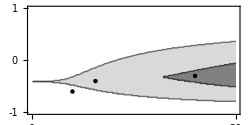

```mathematica
savePanels[{"Fig4D.png"},ticksSqrt=Table[{i^2,If[Mod[i,1]==0,IntegerPart[i],""],If[Mod[i,1]==0,0.02,0.01]},{i,0,10,0.1}];ticksSqrtSlnt=Table[{i^2,"",If[Mod[i,1]==0,0.02,0.01]},{i,0,10,0.1}];ticksBase=Table[{i,If[Mod[i,10]==0,IntegerPart[i],""],If[Mod[i,10]==0,0.02,0.02/3]},{i,0,40,1}];ticksBaseSlnt=Table[{i,"",If[Mod[i,10]==0,0.02,0.02/3]},{i,0,40,1}];points={{4,-0.6},{6.25,-0.4},{16,-0.3}};Show[boundaryPlot,ListPlot[points,PlotStyle->Black],PlotStyle->Black,GridLines->{{},{}},Method->{"GridLinesInFront"->False},FrameTicks->{{{-1,0,1},None},{ticksBase,ticksSqrt}},ImageSize->250,AspectRatio->1/2,FrameLabel->{"",""},PlotRange->{{0,20},{-1,1}},Frame->True,PlotRangePadding->0]]
```

## Spines

Spine voltage and front anchoring at different neck resistances.

### Checking drift

#### checkDriftSigSpine

checkDriftSigSpine classifies front drift with explicit spine heads and neck resistance. kirOnDen selects shaft or head GIRK channels; uinit and uinith set the initial shaft and head voltages.

```mathematica
checkDriftSigSpine[repval_, kirOnDen_, m_, offset_ : -0.5 * Δx] :=
  Module[{nN, nm, xs, vars, spineIndices, spineVars, uinit, uinith, holdTime, eqs, eqsh, tlim, ndsol,
     rmax},
    nN =
      Which[
        (Δx / ℓ //. repval) ^ 2 < 2,
          20
        ,
        (Δx / ℓ //. repval) ^ 2 < 6,
          10
        ,
        True,
          5
      ];
    nm = nN * m + Floor[m / 2];
    xs = Range[-nm, nm];
    vars = Table[u[i][t], {i, -nm, nm}];
    spineIndices = Table[i, {i, (-nN) * m, nN * m, m}];
    spineVars = Table[uh[i][t], {i, spineIndices}];
    uinit[x_] := -Tanh[(x + offset) / (2 * ℓ)];
    uinith[x_] := -(2 * UnitStep[(x + offset) / (2 * ℓ)] - 1);
    eqs =
      Table[
        τ * Derivative[1][u[i]][t] ==
          If[MemberQ[spineIndices, i],
              (m * (uh[i][t] - u[i][t])) / (Subscript[R, nck] * Subscript[G, c])
              ,
              0
            ] + kirOnDen * (1. - 𝓇) * Subscript[f, GIRK][u[i][t]] +
            m^2 * (ℓ / Δx) ^ 2 *
              (
                If[i < nm,
                    u[i + 1][t]
                    ,
                    u[i][t]
                  ] +
                  If[i > -nm,
                    u[i - 1][t]
                    ,
                    u[i][t]
                  ] - 2. * u[i][t]
              )
        ,
        {i, -nm, nm}
      ];
    holdTime = 10;
    eqsh = Table[τh * Derivative[1][uh[i]][t] == (1/2) * (Tanh[(t + 20 - holdTime) * 100] + 1) * ((1.
       + 𝓇) * Subscript[f, NMDA][uh[i][t]] + (1. - kirOnDen) * (1. - 𝓇) * Subscript[f, GIRK][uh[i][t]] + (u[
      i][t] - uh[i][t]) / (Subscript[R, nck] * Subscript[G, c])), {i, spineIndices}];
    tlim = 20;
    ndsol = NDSolve[Evaluate[Flatten[{eqs, eqsh, Table[u[i][-20] == uinit[(xs[[i + nm + 1]] * Δx) / m
      ], {i, -nm, nm}], Table[uh[i][-20] == uinith[(xs[[i + nm + 1]] * Δx) / m], {i, spineIndices}]} //. repval
      ]], Join[vars, spineVars], {t, -20, tlim}];
    If[(u[-nm][t] /. ndsol /. {t -> tlim})[[1]] < 0,
      Return[r]
    ];
    If[(u[nm][t] /. ndsol /. {t -> tlim})[[1]] > 0,
      Return[p]
    ];
    rmax = MaximalBy[Evaluate[Table[(u[i][t] /. ndsol /. {t -> tlim})[[1]], {i, -nm, nm}]] - Evaluate[
      Table[(u[i][t] /. ndsol /. {t -> 0.75 * tlim})[[1]], {i, -nm, nm}]], Abs][[1]];
    If[rmax > 0.1,
      p
      ,
      If[rmax < -0.1,
        r
        ,
        s
      ]
    ]
  ];
```

#### Parameter sweep

calculateAnchoring sweeps spacing, conductance imbalance and neck resistance, then saves the Figure 6A anchoring grid.

```mathematica
calculateAnchoring[placement_,onShaft_,mesh_,depth_:8]:=Module[{bounds,values,coordinates,folder},bounds={{0.1,5.},{-0.99,0.99},{0.01,12.}};{values,coordinates}=theCut[checkDriftSigSpine[{Δx->√#1 ℓ,𝓇->#2,Subscript[R, nck]->#3/Subscript[G, c],τ->0.001,τh->0.001},onShaft,mesh]&,{{RsGc,0.1,5.},{𝓇,-0.99,0.99},{RnckGc,0.01,12.}},4,depth,{r,s,p}];folder=FileNameJoin[{paperRoot,"Figure6","results"}];If[!DirectoryQ[folder],CreateDirectory[folder]];Export[FileNameJoin[{folder,"A_"<>placement<>".json"}],Association["classes"->(values/.{r->0,s->1,p->0}),"bounds"->bounds,"depth"->depth],"RawJSON"]];
```

#### Figure formatting

SurfaceOutline draws surface perimeters. PropagationSurface formats the propagation boundaries. FormatSurface loads and formats each Figure 6 grid.

```mathematica
SurfaceOutline[vertices_,primitives_,upper_:None]:=Module[{faces,edges,counts,boundary},faces=Flatten[Cases[primitives,Polygon[p_,___]:>If[VectorQ[p,IntegerQ],{p},p],∞],1];edges=Flatten[(Partition[Append[#1,First[#1]],2,1]&)/@faces,1];counts=Counts[Sort/@edges];boundary=Keys[Select[counts,#1==1&]];If[upper=!=None,boundary=Select[boundary,Function[edge,!And@@(Abs[vertices⟦#1,3⟧-upper]<1/10^9&)/@edge]]];{Black,Opacity[1],AbsoluteThickness[0.6],Line[boundary]}];PropagationSurface[data_]:=Module[{bounds=data["bounds"],values,graphs,g,top,topLines,contour,field,lines,rmin,rmax,xmax,zmax,gridX,grid,secondary,physical,label,xTicks,rTicks,zTicks,boxLines,marks,conversion=0.23059782865759065},{rmin,rmax}=-Reverse[bounds⟦2⟧];xmax=bounds⟦1,2⟧;zmax=bounds⟦3,2⟧+0.001;values=Reverse[data["classes"],{2}];graphs=Table[field=Map[N[Boole[#1≥0&&BitAnd[#1,bit]>0]]&,values,{3}];If[Min[field]==Max[field],Graphics3D[{}],ListContourPlot3D[field{3,2,1},DataRange->{bounds⟦1⟧,{rmin,rmax},bounds⟦3⟧},Contours->{0.5},ContourStyle->Directive[If[bit==1,RGBColor[0.13, 0.72, 0.26],RGBColor[0.85, 0.15, 0.18]],Opacity[0.25]],MeshFunctions->{#3&},Mesh->{{0.02,0.365,0.71,1.055,1.4}},MeshStyle->Directive[If[bit==1,RGBColor[0.2, 1, 0.25],RGBColor[0.85, 0.15, 0.18]],AbsoluteThickness[1.2]],BoundaryStyle->None,Lighting->"Neutral",PlotRange->All]],{bit,{1,2}}];g=Show[graphs];top=values⟦All,All,-1⟧;topLines=Table[field=Map[Boole[#1≥0&&BitAnd[#1,bit]>0]&,top,{2}];contour=ListContourPlot[Transpose[field],DataRange->{bounds⟦1⟧,{rmin,rmax}},Contours->{0.5},ContourShading->None,Mesh->None,PlotRange->All];Cases[Normal[contour],Line[p_]/;MatrixQ[p,NumericQ]:>p,∞],{bit,{1,2}}];g=Show[g,Graphics3D[Table[{Directive[If[i==1,RGBColor[0.2, 1, 0.25],RGBColor[0.85, 0.15, 0.18]],AbsoluteThickness[1.2]],(Line[(Append[#1,bounds⟦3,2⟧]&)/@#1]&)/@topLines⟦i⟧},{i,2}]]];g=g/.GraphicsComplex[v_,p_,opts___]:>GraphicsComplex[v,{First[p],SurfaceOutline[v,p,bounds⟦3,2⟧],Sequence@@Rest[p]},opts];gridX={0,2.5/conversion,xmax};grid={Line[{{gridX⟦2⟧,rmin,0},{gridX⟦2⟧,rmin,zmax},{gridX⟦2⟧,rmax,zmax},{gridX⟦2⟧,rmax,0},{gridX⟦2⟧,rmin,0}}],Line[{{xmax,rmin,0},{xmax,rmin,zmax},{xmax,rmax,zmax}}]};g=Show[g,Graphics3D[{GrayLevel[0.85],AbsoluteThickness[0.7],grid,Line[{{First[gridX],rmin,zmax},{Last[gridX],rmin,zmax}}]}]];boxLines={Line[{{0,rmin,0},{0,rmin,zmax},{0,rmax,zmax},{0,rmax,0},{0,rmin,0}}],Line[{{xmax,rmin,0},{xmax,rmax,0},{xmax,rmax,zmax}}],Line[{{0,rmin,0},{xmax,rmin,0}}],Line[{{0,rmax,0},{xmax,rmax,0}}],Line[{{0,rmax,zmax},{xmax,rmax,zmax}}]};marks=Join[Table[Line[{{x,rmin,0},{x,rmin,If[Mod[x,10]==0,0.02,0.01] zmax}}],{x,0,Floor[xmax]}],Table[Line[{{0,-r,zmax},{0,-r,zmax 0.988}}],{r,{-0.8,-0.4,0,0.4}}],Table[Line[{{0,rmin,z},{0.008 xmax,rmin,z}}],{z,{0,0.7,1.4}}]];g=Show[g,Graphics3D[{GrayLevel[0.4],Opacity[1],AbsoluteThickness[0.5],boxLines,marks}]];label[t_]:=Style[t,14,FontFamily->"Helvetica",FontSlant->Plain,Black,Opacity[1]];xTicks=Table[{x,If[Mod[x,10]==0,label[x],""],0},{x,0,Floor[xmax]}];rTicks=Table[{-r,Style[Switch[r,-0.4,"−.4",0.4,".4",_,r],10,Black,Opacity[1]],0},{r,{-0.8,-0.4,0,0.4}}];zTicks=Table[{z,label[z],0},{z,{0,0.7,1.4}}];secondary=Graphics3D[{Black,AbsoluteThickness[0.7],Table[With[{x=q/conversion},{Line[{{x,rmax,zmax},{x,rmax+0.03,zmax}}],Text[label[q],{x,rmax,zmax},{0,If[q==0,-3.,-1.7]}]}],{q,{0,2.5,5}}],Text[label[Subscript["R", "s"]Subscript["G", "c"]],{xmax/2,rmax,zmax},{0,-4.5}]}];physical=Graphics3D[{Black,AbsoluteThickness[0.7],Table[{Line[{{xmax,rmax,a},{xmax 0.984,rmax,a}}],Text[label[a],{xmax,rmax,a},{-1.6,0}]},{a,{0,0.7,1.4}}],Text[label[Subscript["G", "AMPA"]" (nS)"],{xmax,rmax,zmax},{-1.1,-4.3}]}];g=Show[g,Graphics3D[{Text[label[Subscript["G", "AMPA"]Subscript["R", "nck"]],{0,rmin,zmax/2},{2,0}]}]];Show[g,secondary,physical,Axes->True,AxesLabel->{label["Δx (µm)"],label["r"],None},AxesEdge->{{-1,-1},{-1,1},{-1,-1}},Ticks->{xTicks,rTicks,zTicks},PlotRange->{{0,xmax},{rmin,rmax},{0,zmax}},PlotRangePadding->Scaled[0.005],PlotRangeClipping->False,ViewPoint->{1.07345684092489,-2.588472601877709,1.2},ViewVertical->{0,0,1},ViewAngle->0.27,Lighting->"Neutral",BoxRatios->{40,20,12},Boxed->False,AxesStyle->Opacity[0],FaceGrids->None,ImageSize->{600,400},ImagePadding->{{65,95},{60,70}},BaseStyle->{FontFamily->"Helvetica",FontSize->14},TicksStyle->Directive[FontFamily->"Helvetica",FontSize->14]]];FormatSurface[folder_,stage_,placement_,directory_:"results"]:=Module[{data,g,bounds,file,rmin,rmax,xmax,grid,label,xTicks,rTicks,zTicks,secondary},file=FileNameJoin[{folder,directory,stage<>"_"<>placement<>".json"}];data=Import[file,"RawJSON"];If[stage=="B",Return[PropagationSurface[data]]];bounds=data["bounds"];xmax=bounds⟦1,2⟧;{rmin,rmax}=-Reverse[bounds⟦2⟧];g=Show[ListContourPlot3D[Reverse[Map[Boole[#1≥0&&BitAnd[#1,1]>0]&,data["classes"],{3}],{2}]{3,2,1},DataRange->{bounds⟦1⟧,{rmin,rmax},bounds⟦3⟧},Contours->{0.5},Mesh->None,ContourStyle->Directive[Gray,Opacity[0.35]]]];g=g/.___->{};g=g/.GraphicsComplex[v_,p_,opts___]:>GraphicsComplex[v,{First[p],SurfaceOutline[v,p],Sequence@@Rest[p]},opts];g=g/.{Opacity[0.38]->Opacity[0.2],GrayLevel[0.55]->GrayLevel[0.5]};grid=Table[Line[{{x,rmin,0},{x,rmin,12.},{x,rmax,12.},{x,rmax,0},{x,rmin,0}}],{x,{bounds⟦1,1⟧,2.5,5}}];g=Show[g,Graphics3D[{GrayLevel[0.85],AbsoluteThickness[0.7],grid}]];label[t_]:=Style[t,14,FontFamily->"Helvetica",FontSlant->Plain,Black];xTicks=Table[{(i/10)^2,If[Mod[i,10]==0,i/10,""],If[Mod[i,10]==0,0.02,0.01]},{i,0,Floor[10 √xmax]}];rTicks=Table[{-r,Switch[r,-0.4,"−.4",0.4,".4",_,r]},{r,{-0.8,-0.4,0,0.4}}];zTicks=Table[{z,z,0.006},{z,{0,4,8,12}}];secondary=Graphics3D[{Black,AbsoluteThickness[0.7],Table[{Line[{{q,rmax,12.},{q,rmax+0.03,12.}}],If[q==0,{},Text[label[q],{q,rmax,12.},{0,-1.7}]]},{q,{0,2.5,5}}],Text[label[Subscript["R", "s"]Subscript["G", "c"]],{xmax/2,rmax,12.},{0,-4.5}]}];Show[g,secondary,Graphics3D[{}],Axes->True,AxesLabel->label/@{"Δx (ℓ)","ΔGc/(2Gc)",Subscript["R", "nck"]Subscript["G", "c"]},AxesEdge->{{-1,-1},{-1,1},{-1,-1}},Ticks->{xTicks,rTicks,zTicks},PlotRange->{{0,xmax},{rmin,rmax},{0,12.}},PlotRangePadding->Scaled[0.005],PlotRangeClipping->False,ViewPoint->{1.,-3.,0.55},ViewVertical->{0,0,1},ViewAngle->0.27,Lighting->Automatic,BoxRatios->{40,20,12},Boxed->{Left,Bottom,Back},FaceGrids->None,ImageSize->{600,400},ImagePadding->{{65,95},{60,70}},BaseStyle->{FontFamily->"Helvetica",FontSize->14},TicksStyle->Directive[FontFamily->"Helvetica",FontSize->14]]];
```

#### Minimum spacing

continuousBands finds continuous imbalance intervals. minimumSpacingData finds the minimum spacing at a 0.1 imbalance tolerance. PropagationMinimumSpacing formats these spacings and intervals. PlotMinimumSpacing loads and plots each summary.

```mathematica
continuousBands[values_, coordinates_, width_] := Select[Split[Flatten[Position[values, True]], #2 == #1 + 1 & ], coordinates[[Last[#1]]] - coordinates[[First[#1]]] >= width - 10^(-12) & ];

minimumSpacingData[data_, width_:0.1] := Module[{classes, bounds, labels, counts, largest, mask, axes, x, y, z, candidates, runs, band}, classes = data["classes"]; bounds = data["bounds"]; labels = MorphologicalComponents[Image3D[Map[Boole[#1 == 1] & , classes, {3}], "Bit"], CornerNeighbors -> True]; counts = KeyDrop[Counts[Flatten[labels]], 0]; If[counts === Association[], Return[{}]]; largest = First[MaximalBy[Keys[counts], counts[#1] & ]]; mask = Map[#1 == largest & , labels, {3}]; axes = MapThread[Subdivide[#1, #2, #3 - 1] & , {bounds[[All,1]], bounds[[All,2]], Dimensions[classes]}]; {x, y, z} = axes; DeleteMissing[Table[candidates = Select[Range[Length[x]], continuousBands[mask[[#1,All,k]], y, width] =!= {} & ]; If[candidates === {}, Missing[], runs = continuousBands[mask[[First[candidates],All,k]], y, width]; band = First[MaximalBy[runs, y[[Last[#1]]] - y[[First[#1]]] & ]]; Association["x" -> x[[First[candidates]]], "z" -> z[[k]], "yRange" -> y[[{First[band], Last[band]}]]]], {k, Length[z]}]]];
PropagationMinimumSpacing[curves_] := Module[
  {colors = {GrayLevel[.42], GrayLevel[.72]}, allLines, lineColors,
   bandLines = {}, bandColors = {}, polygons = {}, low, high, bandPlot, linePlot,
   ticks, leftTicks, common, label, leftWidth = 127.75, rightWidth = 205.4,
   totalWidth, conversion = .23059782865759065},
  label[t_] := Style[t, 14, FontFamily -> "Helvetica", FontSlant -> Plain, Black];
  allLines = Table[({#["x"], #["z"]} & /@ curve), {curve, curves}];
  lineColors = Directive[#, AbsoluteThickness[1.5]] & /@ colors;
  Do[
    low = {First[#["yRange"]], #["z"]} & /@ curves[[i]];
    high = {Last[#["yRange"]], #["z"]} & /@ curves[[i]];
    bandLines = Join[bandLines, {low, high}];
    bandColors = Join[bandColors,
      ConstantArray[Directive[colors[[i]], AbsoluteThickness[.5]], 2]];
    AppendTo[polygons, {colors[[i]], Opacity[.3], Polygon[Join[low, Reverse[high]]]}],
    {i, Length[curves]}];
  common = {Frame -> True, Axes -> False,
    FrameStyle -> Directive[GrayLevel[.25], AbsoluteThickness[.6]],
    BaseStyle -> {FontFamily -> "Helvetica", FontSize -> 12},
    FrameTicksStyle -> Directive[FontFamily -> "Helvetica", FontSize -> 12],
    PlotRangePadding -> 0};
  ticks = Table[{k/10, Switch[k, 0, 0, 14, 1.4, _, ""],
    If[Mod[k, 10] == 0, .036, .012]}, {k, 0, 14}];
  leftTicks = ReplacePart[#, 3 -> #[[3]]*153.4/69.75] & /@ ticks;
  bandPlot = Show[
    ListLinePlot[bandLines, Evaluate[Sequence @@ common], PlotStyle -> bandColors,
      PlotRange -> {{-.9, .55}, {0, 1.4}},
      FrameLabel -> {{label[Row[{Subscript["G", "AMPA"], Subscript["R", "nck"]}]], None},
                    {None, label["r"]}},
      FrameTicks -> {{leftTicks, None}, {None, {{-.8, ""}, {-.4, "−.4"}, {0, 0}, {.4, ".4"}}}},
      AspectRatio -> 161/69.75, ImageSize -> {leftWidth, 250},
      ImagePadding -> {{50, 8}, {44, 45}}], Graphics[polygons]];
  linePlot = ListLinePlot[allLines, Evaluate[Sequence @@ common], PlotStyle -> lineColors,
    PlotRange -> {{0, 5/conversion}, {0, 1.4}},
    FrameLabel -> {{None, label[Row[{Subscript["G", "AMPA"], " (nS)"}]]},
      {label["Δx (µm)"], label[Row[{Subscript["R", "s"], Subscript["G", "c"]}]]}},
    FrameTicks -> {{None, ticks},
      {Table[{x, If[MemberQ[{0, 20}, x], x, ""], If[Mod[x, 10] == 0, .036, .012]},
         {x, 0, 21}], Table[{q/conversion, q}, {q, {0, 2.5, 5}}]}},
    AspectRatio -> 161/153.4, ImageSize -> {rightWidth, 250},
    ImagePadding -> {{7, 45}, {44, 45}}];
  totalWidth = leftWidth + rightWidth;
  Graphics[{Inset[bandPlot, {0, 0}, {Left, Bottom}, {leftWidth, 250}],
    Inset[linePlot, {leftWidth, 0}, {Left, Bottom}, {rightWidth, 250}]},
    PlotRange -> {{0, totalWidth}, {0, 250}}, PlotRangePadding -> 0,
    ImagePadding -> 0, AspectRatio -> 250/totalWidth, ImageSize -> {totalWidth, 250}]
];

PlotMinimumSpacing[stage_, directory_:"results"] := 
   Module[{curves, colors = {GrayLevel[0.4], GrayLevel[0.7]}, main, bands, 
     low, high, range, folder, rTicks, yTicks, silentY, xTicks, maximum}, 
    folder = figureFolder[6]; curves = Table[minimumSpacingData[
        Import[FileNameJoin[{folder, directory, StringJoin[stage, "_", 
            placement, ".json"]}], "RawJSON"]], {placement, 
        {"shaft", "head"}}]; If[stage == "B", Return[PropagationMinimumSpacing[curves]]];
     main = Table[({#1["x"], #1["z"]} & ) /@ curve, 
       {curve, curves}]; bands = MapThread[Function[{curve, color}, 
        If[curve === {}, {}, low = ({First[#1["yRange"]], #1["z"]} & ) /@ 
            curve; high = ({Last[#1["yRange"]], #1["z"]} & ) /@ curve; 
          {color, Opacity[0.2], Polygon[Join[low, Reverse[high]]], 
           Opacity[1], Thin, Line[low], Line[high]}]], {curves, colors}]; 
     range = If[stage == "A", {0, 12}, {0, 1.4}]; 
     maximum = If[stage == "A", 5., 21.682771382138135]; 
     rTicks = Table[{v, Switch[v, -2/5, "−.4", 0, "0", 2/5, ".4", _, 
         ""], {0.02, 0}}, {v, Range[-9, 9]/10}]; 
     yTicks = If[stage == "A", Table[{v, v, {0.02, 0}}, {v, {0, 4, 8, 12}}], 
       Table[{v, v, {0.02, 0}}, {v, {0, 0.6, 1.2}}]]; 
     silentY = ({#1[[1]], "", #1[[3]]} & ) /@ yTicks; 
     xTicks = If[stage == "A", Table[{(i/10)^2, If[Mod[i, 10] == 0, i/10, 
          ""], {0.02, 0}}, {i, 0, 22}], Table[{i, If[Mod[i, 10] == 0, i, ""], 
         {0.02, 0}}, {i, 0, 21}]]; 
     Grid[{{Graphics[bands, Frame -> True, PlotRange -> {All, range}, 
         FrameLabel -> None, FrameTicks -> {{yTicks, None}, {rTicks, None}}, 
         BaseStyle -> {FontFamily -> "Helvetica", FontSize -> 8}, 
         ImageSize -> {75, 150}, ImagePadding -> {{15, 5}, {15, 4}}, 
         AspectRatio -> Full], ListLinePlot[main, PlotStyle -> colors, 
         Frame -> True, PlotRange -> {{0, maximum}, range}, 
         FrameLabel -> None, FrameTicks -> {{silentY, None}, {xTicks, None}}, 
         BaseStyle -> {FontFamily -> "Helvetica", FontSize -> 8}, 
         ImageSize -> {150, 150}, ImagePadding -> {{5, 5}, {15, 4}}, 
         AspectRatio -> Full]}}, Spacings -> {0, 0}]];
```

#### Fig. 6Ai

```mathematica
calculateAnchoring["shaft",1,10]
```

```mathematica
savePanel[figureFolder[6],"Ai",FormatSurface[figureFolder[6],"A","shaft",figureData[6]]]
```

-Graphics3D-

#### Fig. 6Aii

```mathematica
calculateAnchoring["head",0,1]
```

```mathematica
savePanel[figureFolder[6],"Aii",FormatSurface[figureFolder[6],"A","head",figureData[6]]]
```

-Graphics3D-

#### Combining the two results into Fig. 6Aiii

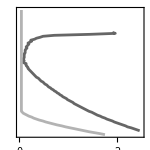
-Graphics- | -Graphics-

```mathematica
savePanel[figureFolder[6],"Aiii",PlotMinimumSpacing["A",figureData[6]]]
```

### Check advancement

The biophysical simulations run in Figure6/run.py.

#### Fig. 6Bi

```mathematica
savePanel[figureFolder[6],"Bi",FormatSurface[figureFolder[6],"B","shaft",figureData[6]]]
```

-Graphics3D-

#### Fig. 6Bii

```mathematica
savePanel[figureFolder[6],"Bii",FormatSurface[figureFolder[6],"B","head",figureData[6]]]
```

-Graphics3D-

#### Combining the two results into Fig. 6Biii

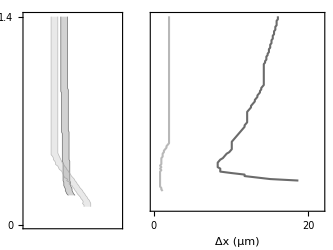

```mathematica
savePanel[figureFolder[6],"Biii",PlotMinimumSpacing["B",figureData[6]]]
```

### Converting to micrometers

The conductance and spacing sweeps run in Figure7/run.py.

#### Figure formatting

PlotFigure7 loads the Python minimum-spacing projections and saves the combined panels. majorX, majorA and majorR select labeled ticks; tickLength, xMarks and yMarks draw them. rgb, lineParts and fillParts color and draw the curves and their projections.

```mathematica
PlotFigure7[folder_, directory_:"results"] :=
  Module[{data, root, w1 = 150, w2 = 75, ht = 100, imagePadding = {{15, 5}, {15, 4}}, aRange, majorLength,
     minorLength, aValues, majorX, majorA, majorR, spacingPadding, tickLength, xMarks, yMarks, rgb, lineParts,
     fillParts, panels, xRange, rRange, xValues, rValues, ticksBase, ticksBaseSlnt, ticksBaseY, ticksBaseYSilent,
     ticksR, ticksRTop, ticksMain, ticksLeft, ticksTop, curves, mainLines, leftLines, leftFill, topLines,
     topFill, hairlines, dualMain, dualTop, color, alpha, p1, p2, pTop, group},
    root = FileNameJoin[{folder, "plots"}];
    If[!DirectoryQ[root],
      CreateDirectory[root]
    ];
    data = Import[FileNameJoin[{folder, directory, "projections.json"}], "RawJSON"];
    aRange = {0, 1.4};
    majorLength = 2.4;
    minorLength = .8;
    aValues = Range[0, 14] / 10;
    majorX[v_] := Mod[v, 5] == 0;
    majorA[v_] := IntegerQ[v];
    majorR[v_] := Mod[10 * v, 4] == 0;
    spacingPadding = {{21, 5}, {15, 4}};
    tickLength[major_] :=
      If[major,
        majorLength
        ,
        minorLength
      ];
    xMarks[values_, major_, y_] := Table[Line[{{v, y}, Offset[{0, tickLength[major[v]]}, {v, y}]}], {
      v, values}];
    yMarks[values_, major_, x_] := Table[Line[{{x, v}, Offset[{tickLength[major[v]], 0}, {x, v}]}], {
      v, values}];
    rgb[q_] := RGBColor @@ q;
    lineParts[parts_] := Join[Line /@ Select[parts, Length[#] > 1&], ({AbsolutePointSize[1.5], Point[
      First[#]]}&) /@ Select[parts, Length[#] == 1&]];
    fillParts[polys_] :=
      If[polys === {},
        {}
        ,
        FilledCurve[({Line[Append[#, First[#]]]}&) /@ polys]
      ];
    panels = <||>;
    Do[
      xRange = data["x_ranges"][placement];
      rRange = data["displayed_r_range"][placement];
      xValues = Range[0, Floor[xRange[[2]]]];
      rValues = Select[Range[-10, 10] / 10, rRange[[1]] <= # <= rRange[[2]]&];
      ticksBase =
        Table[
          {
            v
            ,
            If[If[placement == "head",
              Mod[v, 10] == 0
              ,
              majorX[v]
            ],
              v
              ,
              ""
            ]
            ,
            {0, 0}
          }
          ,
          {v, xValues}
        ];
      ticksBaseSlnt = ({#[[1]], "", {0, 0}}&) /@ ticksBase;
      ticksBaseY =
        Table[
          {
            v
            ,
            If[majorA[v],
              v
              ,
              ""
            ]
            ,
            {0, 0}
          }
          ,
          {v, aValues}
        ];
      ticksBaseYSilent = ({#[[1]], "", {0, 0}}&) /@ ticksBaseY;
      ticksR =
        Table[
          {
            v
            ,
            Switch[v,
              -2/5,
                "-.4"
              ,
              0,
                "0"
              ,
              2/5,
                ".4"
              ,
              _,
                ""
            ]
            ,
            {0, 0}
          }
          ,
          {v, rValues}
        ];
      ticksRTop = ({-#[[1]], #[[2]], {0, 0}}&) /@ ticksR;
      ticksMain = {Black, AbsoluteThickness[.5], xMarks[xValues, majorX, 0], yMarks[aValues, majorA, 
        0]};
      ticksLeft = {Black, AbsoluteThickness[.5], xMarks[rValues, majorR, 0], yMarks[aValues, majorA, 
        rRange[[1]]]};
      ticksTop = {Black, AbsoluteThickness[.5], xMarks[xValues, majorX, -rRange[[2]]], yMarks[-rValues,
         majorR, 0]};
      curves = Select[data["curves"], #["placement"] == placement&];
      curves = SortBy[curves, #["width"]&];
      mainLines = {};
      leftLines = {};
      leftFill = {};
      topLines = {};
      topFill = {};
      hairlines = {};
      dualMain =
        If[placement == "head",
          {Black, AbsoluteThickness[.35], Line[{{10 / 1.4, aRange[[1]]}, {10 / 1.4, aRange[[2]]}}]}
          ,
          {}
        ];
      dualTop =
        If[placement == "head",
          {Black, AbsoluteThickness[.35], Line[{{10 / 1.4, -rRange[[2]]}, {10 / 1.4, -rRange[[1]]}}]}
            
          ,
          {}
        ];
      Do[
        color = rgb[q["color"]];
        alpha =
          If[q["width"] == .1,
            .12
            ,
            .08
          ];
        AppendTo[mainLines, {color, Thickness[.01], lineParts[q["main"]]}];
        AppendTo[leftLines, {color, Thin, lineParts[q["left_lines"]]}];
        AppendTo[leftFill, {color, Opacity[alpha], fillParts[q["left_polygons"]]}];
        AppendTo[topLines, {color, Thin, lineParts[q["top_lines"]]}];
        AppendTo[topFill, {color, Opacity[alpha], fillParts[q["top_polygons"]]}];
        If[q["width"] == .1,
          AppendTo[hairlines, {rgb[q["reference_color"]], AbsoluteThickness[.35], Line[q["hairline"]]
            }]
        ]
        ,
        {q, curves}
      ];
      p1 = Show[ListLinePlot[{}, Frame -> True, FrameLabel -> None, PlotRange -> {xRange, aRange}, ImageSize
         -> {w1, ht}, AspectRatio -> Full, FrameTicks -> {{ticksBaseYSilent, None}, {ticksBase, None}}, FrameTicksStyle
         -> Black, ImagePadding -> spacingPadding, Axes -> False, Background -> None], Graphics[{mainLines, dualMain,
         ticksMain}]];
      p2 = Show[ListLinePlot[{}, Frame -> True, FrameLabel -> None, PlotRange -> {rRange, aRange}, ImageSize
         -> {w2, ht}, AspectRatio -> Full, FrameTicks -> {{ticksBaseY, None}, {ticksR, None}}, FrameTicksStyle
         -> Black, ImagePadding -> imagePadding, Axes -> False, Background -> None], Graphics[{leftFill, leftLines,
         ticksLeft}]];
      pTop = Show[ListLinePlot[{}, Frame -> True, FrameLabel -> None, PlotRange -> {xRange, {-rRange[[
        2]], -rRange[[1]]}}, ImageSize -> {w1, w2}, AspectRatio -> Full, FrameTicks -> {{ticksRTop, None}, {ticksBaseSlnt,
         None}}, FrameTicksStyle -> Black, ImagePadding -> spacingPadding, Axes -> False, Background -> None],
         Graphics[{topFill, topLines, hairlines, dualTop, ticksTop}]];
      group = <|"main" -> p1, "left" -> p2, "top" -> pTop|>;
      AssociateTo[panels, placement -> group];
      Do[Export[FileNameJoin[{root, placement <> "_" <> part <> ".svg"}], group[part], "SVG"], {part,
         {"main", "left", "top"}}];
      ,
      {placement, {"shaft", "head"}}
    ];
    Row[Table[Grid[{{Spacer[{75, 75}], panels[p]["top"]}, {panels[p]["left"], panels[p]["main"]}}, Spacings
       -> {0, 0}], {p, {"shaft", "head"}}]]
  ];
```

#### Fig. 7

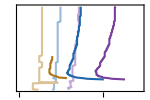
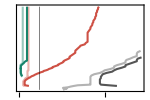
| -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
PlotFigure7[figureFolder[7],figureData[7]]
```

## Figure 1

Generated in Python: Figure1/run.py

## Figure 8

Generated in Python: Figure8/run.py

## Supplementary Figure 1

Generated in Python: SupplementaryFigure1/run.py

## Supplementary Figure 2

Calculate electrotonic length and plot its contours across dendritic diameter and channel conductance density.

```mathematica
lc=1/(√(((𝒢c nS) ℛs)/μm))/.ℛs->Rax/(π ((d μm)/2)^2)/.Rax->(400 Ω cm (10^4 μm))/((10^9 nS Ω) cm);
```

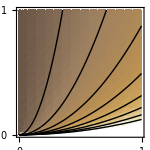

```mathematica
savePanels[{"FigS2.svg"},ticks=Table[{i,If[Mod[i,1]==0,IntegerPart[i],""],If[Mod[i,0.1]==0,0.02,0.01]},{i,0,1,0.05}];Show[DensityPlot[lc/.μm->1,{d,0,1},{𝒢c,0,1},ColorFunction->"CoffeeTones",FrameLabel->None,ImageSize->150,FrameTicks->{{ticks,{}},{ticks,{}}}],ContourPlot[lc/.μm->1,{d,0,1},{𝒢c,0,1},Contours->Range[5,40,5],ContourShading->False,ContourStyle->Black,Frame->False,Axes->False]]]
```

## Supplementary Figure 3

Generated in Python: SupplementaryFigure3/run.py

## Supplementary Figure 4

Generated in Python: SupplementaryFigure4/run.py

## Supplementary Figure 5

Generated in Python: SupplementaryFigure5/run.py

## Supplementary Figure 6

Generated in Python: SupplementaryFigure6/run.py

## Supplementary Figure 7

Generated in Python: SupplementaryFigure7/run.py